```mathematica
(*Old data *)
(*data={{0.3008,0.4106,0.3934,0.2798,0.1786,0.013,0.0154,0.074,0.0022,0.05},{0.3984,0.2678,0.071,0.0072,0.0006,0.0686,0.0206,0.0172,0.0432,0.0072},{0.3888,0.0674,0.0828,0.0434,0.099,0.003,0.025,0.0282,0.057,0.0926},{0.0644,0.0062,0.0012,0.0346,0.011,0.0742,0.0374,0.0102,0.0826,0.0528},{0.0836,0.0766,0.0238,0.0196,0.2168,0.1022,0.0052,0.0294,0.1264,0.0364},{0.0216,0.0762,0.0152,0.0072,0.03,0.0698,0.0016,0.1034,0.0892,0.0786},{0.032,0.1682,0.0036,0.0066,0.061,0.0638,0.112,0.0678,0.0036,0.0048},{0.1054,0.0952,0.0058,0.0436,0.0268,0.0996,0.0112,0.0952,0.1466,0.0418},{0.166,0.0704,0.0734,0.0302,0.0282,0.0702,0.0162,0.0148,0.0248,0.0108}};*)

data1 = {
{0.3968,0.3356,0.4144,0.3642,0.2664,0.2298,0.1718,0.1134,0.0756,0.0882},{0.4018,0.3856,0.1862,0.133,0.0322,0.0624,0.0046,0.0892,0.0544,0.0504},{0.3966,0.0858,0.004,0.0058,0.0158,0.034,0.0298,0.0012,0.031,0.0044},{0.3504,0.0222,0.038,0.0002,0.0336,0.0128,0.1258,0.0068,0.0154,0.0488},{0.1058,0.0014,0.0146,0.0036,0.0002,0.0034,0.0116,0.0802,0.0168,0.0758},{0.1476,0.1584,0.0626,0.0544,0.0102,0.0916,0.004,0.0944,0.0066,0.0918},{0.0044,0.0364,0.0158,0.0264,0.085,0.0034,0.016,0.0384,0.0428,0.014}
};

data2 = {
{11,11,12,11,8,8,7,7,8,11},
{12,11,9,12,0,0,0,0,1,0},
{12,11,1,0,0,0,0,0,0,0},
{10,0,0,0,0,0,0,0,0,0},
{7,0,0,0,0,0,0,0,0,0},
{0,1,0,0,0,0,0,0,0,0},
{1,0,0,0,0,0,0,0,0,0}
};

plot1=MatrixPlot[data1, 
ColorFunction->ColorData["TemperatureMap"],
ColorFunctionScaling->True,
PlotLegends->Automatic, 
LabelStyle->Directive[FontSize->20, Black, Bold],
PlotLabel->Style[Row@{"A) Disease peak difference",Spacer[200]}, FontSize->22, FontColor->Black, FontFamily -> "Century"],
FrameLabel->{Style["Planning horizon (days)", Black, 20 , FontFamily -> "Century"], Style["Population Risk Sensitivity", Black, 20, FontFamily -> "Century"]},
Frame->True,
FrameTicks->{{{{1, 5},{2,10},{3,15},{4,20},{5,25},{6,30},{7,35}},None},{{{1,0.01},{3,0.03},{5,0.05},{7,0.07},{9,0.09}},{{1,None}}}},
ImageSize-> {490,490}
];

plot2=MatrixPlot[data2, 
ColorFunction->ColorData["TemperatureMap"],
ColorFunctionScaling->True,
PlotLegends->Automatic, 
LabelStyle->Directive[FontSize->20, Black, Bold],
(*PlotLabel->Style[Row@{"A) Avg. max. behavior change day difference",Spacer[8]}, FontSize->22, FontColor->Black, FontFamily -> "Century"],*)
FrameLabel->{Style["Planning horizon (days)", Black, 20, FontFamily -> "Century" ], Style["Population Risk Sensitivity", Black, 20, FontFamily -> "Century"]},
Frame->True,
FrameTicks->{{{{1, 5},{2,10},{3,15},{4,20},{5,25},{6,30},{7,35}},None},{{{1,0.01},{3,0.03},{5,0.05},{7,0.07},{9,0.09}},{{1,None}}}},
ImageSize-> {490,490}
];

plot  = GraphicsRow[{plot1, plot2}, ImageSize->1200];
(*Export["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/adaptive_networks/Figures/article_figures/min_avg_reduction_day_lag_disease_peak_diference.pdf",plot,"PDF","AllowRasterization"->False]*)
plot (* min_avg_reduction_day_lag_disease_peak_diference*)
```

-Graphics-

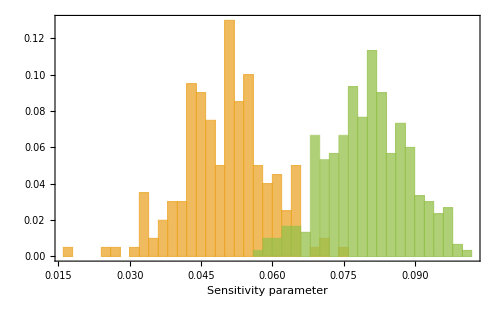
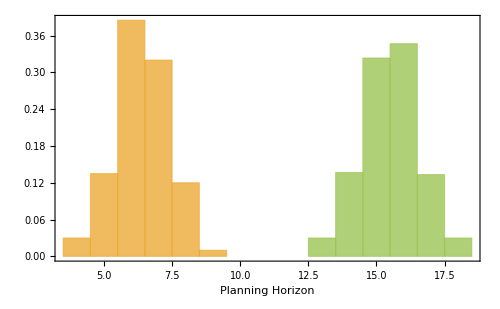
{{Null^9 -Graphics- -Graphics-},{□}}

```mathematica
{{n = 500;
data1T={6,6,7,5,7,7,6,6,6,8,7,8,6,6,6,6,7,6,9,8,6,6,4,6,6,9,6,7,5,6,8,7,
6,6,4,8,5,8,6,7,6,6,6,7,5,7,5,6,6,6,7,7,7,5,6,6,6,7,6,7,6,5,7,7,6,6,8,8,8,6,6,7,5,8,8,7,6,7,4,8,
7,7,6,4,7,6,6,7,7,6,7,8,7,5,7,7,6,6,7,7,6,6,7,6,7,8,8,7,7,7,6,7,8,5,6,5,7,6,6,5,7,6,8,8,7,6,6,5,
8,6,7,7,7,7,8,5,6,8,7,6,7,7,5,6,7,6,5,5,6,7,4,6,7,5,6,7,5,6,6,6,6,7,6,6,8,5,5,6,6,6,6,6,7,7,5,6,
4,7,5,7,7,6,6,7,7,7,6,7,5,6,8,7,5,6,5,5,7,8,6,7};
data2T={16,16,16,17,17,17,17,17,15,16,14,15,13,16,15,16,18,16,16,14,16,17,16,16,16,15,16,15,13,14,16,15,14,
15,16,16,16,15,16,15,17,15,14,13,15,16,16,16,16,17,17,16,16,15,15,16,17,16,16,16,15,15,18,15,15,16,16,15,
14,17,15,16,17,15,16,16,13,16,18,14,15,16,17,16,15,15,15,16,16,16,16,13,14,15,16,16,17,15,14,18,16,18,15,
18,14,15,15,16,15,15,15,15,14,16,16,16,15,16,17,16,16,16,17,16,15,16,15,14,14,17,15,15,16,15,14,15,16,14,
14,15,14,17,16,15,14,18,15,17,14,15,15,14,15,14,15,15,15,15,16,15,15,15,16,15,15,16,16,16,18,17,16,15,15,
17,16,15,15,14,16,16,17,16,14,16,16,16,14,15,15,15,15,14,14,16,14,16,16,16,16,15,17,15,15,14,15,16,15,15,
14,15,17,17,17,16,15,14,16,14,17,15,16,16,15,15,15,16,16,15,15,16,15,16,14,17,15,16,15,13,17,14,15,16,13,
16,15,15,15,14,17,15,17,16,16,16,14,17,18,16,15,16,15,17,13,16,16,16,15,17,16,17,15,14,17,14,15,17,16,16,
15,17,13,17,14,14,15,16,15,14,15,16,16,14,16,15,16,16,17,16,15,15};

data1V={0.0448660532132682,0.0516821180201742,0.0448715537787888,0.0507753033343336,0.0503577056109036,0.0638341391970091,
0.0433147923871066,0.0512588482192074,0.0512100331998743,0.0373720262187334,0.0542479242888881,0.0529226687105742,
0.0646762166784813,0.0452252344432943,0.0313632744177301,0.0561094211449824,0.0523965244720767,0.0599081934265497,
0.0452111866792487,0.0581865759145621,0.05049331498436,0.054470482451039,0.04020761970248,0.0501644450944474,
0.0714930047233998,0.0648530408469522,0.0566849167717201,0.0545506534209482,0.0622670939360819,0.0508806047630823,
0.048463983505485,0.0545155990967598,0.0447934967890808,0.0609050721012747,0.0394846769006893,0.0331077166573506,
0.0434341765886598,0.0531883494547846,0.0536823623512632,0.0420679943301857,0.0502663566005928,0.0455875764680271,
0.0336853594260725,0.0415668142597098,0.0445050773428814,0.0430100603388719,0.0439646767325739,0.0266327768990899,
0.0519577954149842,0.0451677703800992,0.0645235491723265,0.0339733389545379,0.05082886580071,0.047927810585102,
0.035804584529902,0.0565034972259748,0.0518684546728009,0.0480827681365389,0.0548095486982508,0.0520242205984093,
0.043393803796321,0.0320599419615204,0.0577825192286028,0.0539104981403719,0.0472995469379877,0.0515920618826144,
0.0463291607924858,0.0551593758398034,0.0549109456385533,0.0559889572627266,0.0486142632104604,0.0524029974322434,
0.069464822299509,0.0554407437382661,0.060423715297309,0.0459089950368619,0.0516296553216032,0.056836783068167,
0.0324302764415851,0.0552508265642768,
0.0467137088583209,0.0431987818399575,0.051311653257322,0.0448461762553811,0.0432809062933714,0.060655505106186,
0.0463495748098325,0.0756848352800169,0.0559224701358719,0.0488864493624091,0.0554271390257959,0.0705988815082733,
0.0526914614405096,0.058908668475098,0.0619058972405827,0.0458754396803312,0.0470409258028562,0.0470442686533244,
0.0643785273010296,0.0537206226919632,0.0501003302057405,0.0629746609981477,0.0644565687518077,0.0478503508517345,
0.0380355985280692,0.0459373689805196,0.0547839163158381,0.0320555743016694,0.0545628014314355,0.044922009561463,
0.0615529737403419,0.0540543646889543,0.0510184485129435,0.0578665281391864,0.0494871271709441,0.0557127716140476,
0.0456202092526205,0.0508168507622901,0.050780608558655,0.0434794335505014,0.050556659747138,0.0425932329634725,
0.0411024340203524,0.0430994173990504,0.0520201523841988,0.0543421783910943,0.0393657317827519,0.0586481914720912,
0.0641032588148091,0.049911011323763,0.0622104488291868,0.0495904670452582,0.0414920979068241,0.0420768864265969,
0.043812414308823,0.0393285630560535,0.0642771255616871,0.0593639911743094,0.0175891946374323,0.0652584012417816,
0.0421766013600558,0.0424001609342774,0.0517085502879841,0.0654826598259256,0.0454864095513872,0.0423080436131053,
0.059698178280925,0.0541693205502301,0.052624223544501,0.0456735806474085,0.0500397360628684,0.0633059116812073,
0.0433613854041534,0.0438062878009779,0.0376318418469716,0.0486812391866603,0.0519343900115483,0.0608654594433926,
0.0437375154323849,0.047657278878637,0.0475371063432299,0.0473765559547524,0.051598883970334,0.0338263281852434,
0.0564359688688092,0.0536324974241023,0.0370461778302189,0.0604571159027772,0.0597259365088284,0.0536508122930827,
0.0467296067015429,0.0519736644386108,0.0574788463571866,0.0531831355853912,0.0399361464303499,0.0500044719670154,
0.0405260979364549,0.0540294295369753,0.061434744843723,0.0581317186554868,0.0640915529470874,0.0456787496064246,
0.0450479271034556,0.0375669458965644,0.0497168019987618,0.0256963574327572,0.0521112200634231,0.0538705338226114,
0.0396745446671297,0.0498177144947074,0.0404302220142882,0.0340623596652691,0.0574834468725177,0.0609013726301292,
0.0568809328462951,0.0559832592511721,0.0466403621955723,0.0539126839250537,0.0472556940686051,0.0477383769107589};

data2V={0.0892612429642387,0.0822532571223568,0.0597183856361044,0.097676011796721,
0.0950526612622844,0.088628398622201,0.0699347499785018,0.0698211556864208,0.0739953944069709,0.088773622346564,0.0915026601299571,0.0865887999338307,
0.0939782159905038,0.075908323374018,0.0825042232856105,0.0782718715755934,0.088749465331234,0.092039733301828,0.0797327092175485,0.0915569197854368,
0.0852474174231923,0.074095902841727,0.0836895986055434,0.0810928535315128,0.0835737772397362,0.0740233250187055,0.0870824886683371,0.0729744113454136,
0.0807883488604753,0.0956051398513065,0.0817460229909048,0.0703267516454756,0.0845482105555048,0.079941376791162,0.0864510105101652,0.0642113094033183,
0.0594440348764745,0.0931599618346243,0.0873306415280308,0.0850060640656102,0.0842689241623292,0.075665004895738,0.0825445484660204,0.0745417081252566,
0.0864274514849361,0.0808436913367492,0.080263134729748,0.0954428218762129,0.080985017546333,0.0883239013204958,0.0693697159683784,0.0696827033574221,
0.0697138229095806,0.0733281492388909,0.0625429155748916,0.0709577130497237,0.0800258299733089,0.0816082949893229,0.0789946553306186,0.087567642723471,
0.0714560779075683,0.07695928437192,0.0908285214253043,0.0794496457324749,0.0712213568468769,0.0694006837721816,0.0715391295399753,0.057686780934122,
0.0780527788388927,0.0827692193798414,0.0607997882131268,0.0992793463101284,0.0824443497342687,0.0638914445738444,0.0735726864775786,0.088883054563003,
0.0787321523481815,0.0797090897431418,0.0720040945325881,0.0652271425230465,0.086259572949123,0.0849674051654035,0.0950576023797241,0.0800027029081212,
0.0807910624481491,0.0696557579362923,0.0881063131518616,0.0904765045234247,0.0836621665468857,0.076657153968672,0.0987004813012741,0.0822154011740289,
0.0761956293435256,0.0666342173058521,0.0658173289158274,0.0617132014646122,0.0864940225498312,0.0766931501691,0.087829540374949,0.0714541205155174,
0.0928628048974385,0.0741439985753597,0.084283052418121,0.0795789550130762,0.0853757949072362,0.0871639763210337,0.0834190674715597,0.0925461702870255,
0.081843874448902,0.0938419528907,0.0844994750245044,0.0773789939065368,0.0833511713229774,0.097304536800369,0.0690133595896457,0.0711179652524723,
0.0631931974709623,0.0818978711001282,0.1004784287713282,0.0741549118800899,0.0963701489773119,0.0772674225282975,0.0908408657906877,0.0887391503458934,
0.0881057515081722,0.0712058612017716,0.0772714348408321,0.0776875918412938,0.0835497946272889,0.0752877293569877,0.0864639258900557,0.0891008266972354,
0.0815800321194277,0.0791941034900559,0.0671934946836823,0.0815557373224428,0.0894723235751733,0.0789756222606051,0.0904487602001025,0.0759752788127895,
0.0873024408526647,0.0899877772409998,0.0783303950284264,0.0656400344679036,0.0709461278878651,0.0776260284702272,0.0812058338696308,0.0865736347542129,
0.0879406444145111,0.0779198475207968,0.0773813240099508,0.0818869946218687,0.0738209207321712,0.0813112002537683,0.0764266218508115,0.0777766112233765,
0.0733052589253078,0.0943652084420009,0.0718684496960261,0.076146825866325,0.0816934290225461,0.0769768720717283,0.0819278482536271,0.0708473126630394,
0.0715985664079784,0.0683084716364179,0.0731045759745202,0.0859602617773229,0.0758399373360679,0.0861752035096458,0.0974731974896705,0.071518966331163,
0.0827628594704793,0.0789932960413755,0.0728099083681854,0.0828515586854995,0.0811695736258241,0.0686468333422489,0.0780711751664261,0.0906187576673047,
0.0837034494026281,0.0764466164811625,0.0743130461361198,0.0816246290887626,0.0778701968201291,0.0795467079287362,0.0703090002166962,0.089778930487953,
0.0775010482552374,0.0691963556132843,0.0944140975887386,0.0727441586515043,0.0834422761369135,0.0880113711664483,0.0797973641011906,0.0865390168000027,
0.0852210569939737,0.0768115924416489,0.0749677422278987,0.0681701811303725,0.0791195214194608,0.0757989022572339,0.0815933368517865,0.0879786703335851,
0.0749390274336553,0.0827321698764948,0.0697698987896374,0.0740966136167733,0.0812239701084319,0.0845938259207566,0.0903680967721934,0.0798774146629366,
0.0815636222632705,0.0622171640559473,0.0831301881164617,0.0681021888215106,0.0840907407361847,0.0803670225640415,0.0976991768417905,0.0797657125906871,
0.0693099934755789,0.0972150146635242,0.0782400968931804,0.0806297486492252,0.0779514952924943,0.0672707059562891,0.0974599069783742,0.0801274831094093,
0.071386042272758,0.0761801055617251,0.0754564864923205,0.0877562009114226,0.0727677803224511,0.0822517005419145,0.085445569025769,0.0911837389911012,
0.0680076683739683,0.0732608867548251,0.0842261183428163,0.0818764047617527,0.080978584057295,0.0683011046727601,0.0681427344636769,0.0871181140925768,
0.0810902054794044,0.084536313942963,0.08770940463844,0.059361320264762,0.076888120090148,0.0682271670608683,0.0673270328875953,0.0685579404931046,
0.0777699101357853,0.0831086250712131,0.0956451009945453,0.0893880729483792,0.0766273570875476,0.0836161090454291,0.0974794326795903,0.0830955869007683,
0.0806397911183045,0.0771672724303739,0.0844930879079979,0.0650849272975744,0.0923803166468732,0.0836609986627033,0.0623835923989137,0.0862957632397047,
0.0812416914090411,0.082632538205209,0.0789709674409461,0.0740700660552635,0.0724506058264826,0.085557968441488,0.0938317941717477,0.0879619264557803,
0.0721054179744316,0.0820039395663827,0.0931233747359602,0.0731713098812918,0.0832891950932039,0.0883486801913795,0.0800290425836234,0.0751347107696457,
0.0802628233804939,0.0782457606542199,0.0764699345691831,0.0737277784829368,0.0880848899586885,0.0797057372419446,0.0761511098159714,0.0733508371329968,
0.0821304063961272,0.0886693602989435,0.0717060602552314,0.0915468650678347,0.0601440160110511,0.0759213895715889,0.0750507852930405,0.0770161259375604};


distplotT= Histogram[{data1T,data2T}, 45, "Probability", 
ChartStyle->{
Opacity[.75, ToColor[RGBColor["#ECA528"],Hue]],
Opacity[.75,ToColor[RGBColor["#96C14B"],Hue]]
},
LabelStyle->Directive[Bold, 22, Black],
Frame->{True,True,False,False},
FrameLabel->{Style["Planning Horizon", FontSize->22, Bold, Black],None},
ImageSize->500,
Axes->False];
Export["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/adaptive_networks/Figures/article_figures/distplotT.pdf",distplotT,"PDF","AllowRasterization"->False];

distplotV= Histogram[{data1V,data2V}, 45, "Probability", 
ChartStyle -> {
Opacity[.75,ToColor[RGBColor["#ECA528"],Hue]],
Opacity[.75,ToColor[RGBColor["#96C14B"],Hue]]
},
LabelStyle->Directive[Bold, 22, Black],
Frame->{True,True,False,False},
FrameLabel->{Style["Sensitivity parameter", FontSize->22, Bold, Black],None},
ImageSize->500,
Axes->False];
Export["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/adaptive_networks/Figures/article_figures/distplotV.pdf",distplotV,"PDF","AllowRasterization"->False];

distplotT
distplotV}, {□}}
```

```mathematica
()
```

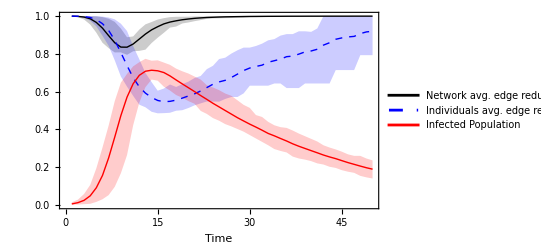

```mathematica
myplot = ListLinePlot[ {

{0.9998,0.9986,0.9951,0.9861,0.9666,0.9363,0.8967,0.8589,0.8359,0.8355,0.8523,0.8786,0.9051,0.9273,0.9441,0.9589,0.9686,0.9752,0.9808,0.9848,0.9883,0.9907,0.9928,0.994,0.9952,0.9962,0.9968,0.9973,0.9978,0.9983,0.9985,0.9988,0.999,0.9991,0.9992,0.9994,0.9995,0.9995,0.9996,0.9997,0.9997,0.9998,0.9998,0.9998,0.9998,0.9998,0.9999,0.9999,0.9999,0.9999},{0.9987,0.9946,0.982,0.9553,0.9123,0.859,0.8307,0.8077,0.8081,0.795,0.8141,0.8159,0.8224,0.8574,0.8857,0.9117,0.9392,0.9448,0.961,0.9664,0.9731,0.979,0.9855,0.9876,0.9882,0.9893,0.9898,0.992,0.992,0.9943,0.9943,0.9947,0.9951,0.9954,0.9963,0.9971,0.9979,0.9981,0.9981,0.9981,0.9984,0.9984,0.9986,0.9986,0.9986,0.9987,0.9989,0.999,0.999,0.999},{1.0,1.0,1.0,1.0,0.999,0.9947,0.9863,0.9696,0.9341,0.8881,0.8926,0.9287,0.9565,0.9688,0.9819,0.9893,0.9947,0.9965,0.9967,0.9971,0.9982,0.9986,0.999,0.9992,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0},{1.0,0.9994,0.9976,0.9928,0.9812,0.9601,0.9244,0.8724,0.8065,0.7381,0.6737,0.6254,0.5921,0.5692,0.5533,0.5466,0.5487,0.5551,0.5657,0.5772,0.5885,0.6037,0.6216,0.6394,0.6517,0.66,0.6749,0.6931,0.7118,0.7252,0.7335,0.7404,0.7558,0.7639,0.7722,0.7853,0.7882,0.7989,0.8106,0.8155,0.8246,0.8465,0.8592,0.8774,0.8847,0.8898,0.8927,0.9073,0.9164,0.9197},{0.9995,0.9977,0.991,0.9757,0.9461,0.896,0.8432,0.7658,0.6799,0.6268,0.5778,0.5311,0.5172,0.4934,0.4852,0.4862,0.4882,0.499,0.5017,0.5132,0.5275,0.538,0.5477,0.5477,0.5469,0.5614,0.5717,0.5717,0.5909,0.6316,0.6316,0.6316,0.6316,0.6432,0.6432,0.619,0.619,0.619,0.6432,0.6432,0.6432,0.6432,0.6432,0.7143,0.7143,0.7143,0.7143,0.7932,0.7932,0.7932},{1.0,1.0,1.0,1.0,0.9995,0.9974,0.9926,0.983,0.9598,0.9211,0.8411,0.7715,0.6989,0.6506,0.6051,0.6163,0.638,0.6247,0.6393,0.653,0.6722,0.683,0.7192,0.737,0.7727,0.7799,0.8017,0.8192,0.8333,0.8333,0.8418,0.8543,0.8719,0.8783,0.8968,0.9048,0.9048,0.9197,0.9197,0.9167,0.9348,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0},{0.0053,0.012,0.0244,0.0482,0.0911,0.1561,0.2488,0.3595,0.4736,0.571,0.6421,0.6866,0.7082,0.7134,0.7104,0.7012,0.6834,0.6619,0.6411,0.6208,0.6004,0.5792,0.5591,0.5382,0.5192,0.5,0.481,0.4619,0.4447,0.4278,0.4122,0.3958,0.3786,0.366,0.352,0.3386,0.3236,0.3107,0.2991,0.2875,0.2761,0.2643,0.2542,0.2452,0.2346,0.2242,0.215,0.2058,0.197,0.1894},{0.002,0.002,0.004,0.006,0.016,0.03,0.052,0.096,0.168,0.264,0.422,0.542,0.624,0.664,0.658,0.626,0.606,0.582,0.568,0.55,0.536,0.498,0.482,0.46,0.446,0.428,0.416,0.402,0.388,0.37,0.352,0.334,0.316,0.296,0.286,0.278,0.256,0.246,0.24,0.232,0.22,0.214,0.202,0.196,0.184,0.176,0.17,0.154,0.146,0.14},{0.014,0.028,0.058,0.106,0.194,0.304,0.42,0.55,0.648,0.694,0.734,0.756,0.774,0.764,0.766,0.754,0.742,0.722,0.708,0.696,0.68,0.664,0.634,0.622,0.608,0.59,0.578,0.554,0.53,0.514,0.476,0.466,0.44,0.422,0.412,0.408,0.394,0.378,0.364,0.35,0.336,0.316,0.304,0.294,0.282,0.268,0.26,0.26,0.246,0.236}

},
Filling->{{1->{3}},1->{2}, {4->{6}},4->{5}, , {7->{9}},7->{8}},
PlotStyle->{Directive[Thick,Black],None,None, Directive[Thick,Dashed,Blue],None,None, Directive[Thick,Red], None, None},
Frame->{True,True,False,False},
FrameLabel->{"Time",None},
Axes->False,
LabelStyle->Directive[Bold, Medium, Black],
TicksStyle->Directive[Bold, 14],PlotRange->{{0,50},{0, 1}},
PlotLegends->Placed[{Style["Network avg. edge reduction", FontFamily -> "Century", 14],None, None,
Style["Individuals avg. edge reduction", FontFamily -> "Century", 14], None, None,
Style["Infected Population", FontFamily -> "Century", 14] }, Below]];
Export["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/adaptive_networks/global_local_resp_dist.pdf",myplot,"PDF","AllowRasterization"->False];
myplot
```

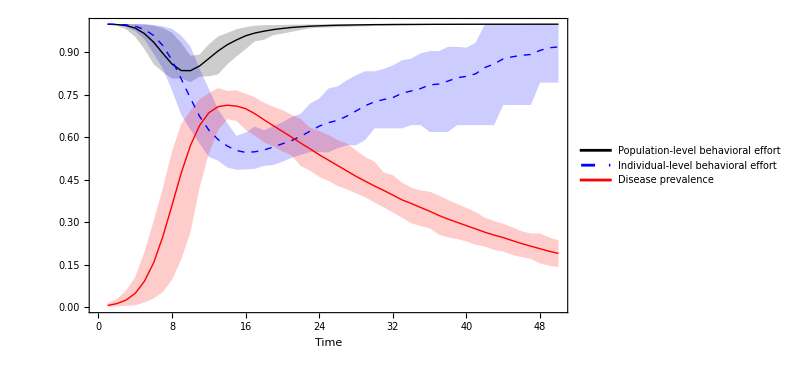

```mathematica
distplot0  = ListLinePlot[ {

{0.9998,0.9986,0.9951,0.9861,0.9666,0.9363,0.8967,0.8589,0.8359,0.8355,0.8523,0.8786,0.9051,0.9273,0.9441,0.9589,0.9686,0.9752,0.9808,0.9848,0.9883,0.9907,0.9928,0.994,0.9952,0.9962,0.9968,0.9973,0.9978,0.9983,0.9985,0.9988,0.999,0.9991,0.9992,0.9994,0.9995,0.9995,0.9996,0.9997,0.9997,0.9998,0.9998,0.9998,0.9998,0.9998,0.9999,0.9999,0.9999,0.9999},{0.9987,0.9946,0.982,0.9553,0.9123,0.859,0.8307,0.8077,0.8081,0.795,0.8141,0.8159,0.8224,0.8574,0.8857,0.9117,0.9392,0.9448,0.961,0.9664,0.9731,0.979,0.9855,0.9876,0.9882,0.9893,0.9898,0.992,0.992,0.9943,0.9943,0.9947,0.9951,0.9954,0.9963,0.9971,0.9979,0.9981,0.9981,0.9981,0.9984,0.9984,0.9986,0.9986,0.9986,0.9987,0.9989,0.999,0.999,0.999},{1.0,1.0,1.0,1.0,0.999,0.9947,0.9863,0.9696,0.9341,0.8881,0.8926,0.9287,0.9565,0.9688,0.9819,0.9893,0.9947,0.9965,0.9967,0.9971,0.9982,0.9986,0.999,0.9992,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0},{1.0,0.9994,0.9976,0.9928,0.9812,0.9601,0.9244,0.8724,0.8065,0.7381,0.6737,0.6254,0.5921,0.5692,0.5533,0.5466,0.5487,0.5551,0.5657,0.5772,0.5885,0.6037,0.6216,0.6394,0.6517,0.66,0.6749,0.6931,0.7118,0.7252,0.7335,0.7404,0.7558,0.7639,0.7722,0.7853,0.7882,0.7989,0.8106,0.8155,0.8246,0.8465,0.8592,0.8774,0.8847,0.8898,0.8927,0.9073,0.9164,0.9197},{0.9995,0.9977,0.991,0.9757,0.9461,0.896,0.8432,0.7658,0.6799,0.6268,0.5778,0.5311,0.5172,0.4934,0.4852,0.4862,0.4882,0.499,0.5017,0.5132,0.5275,0.538,0.5477,0.5477,0.5469,0.5614,0.5717,0.5717,0.5909,0.6316,0.6316,0.6316,0.6316,0.6432,0.6432,0.619,0.619,0.619,0.6432,0.6432,0.6432,0.6432,0.6432,0.7143,0.7143,0.7143,0.7143,0.7932,0.7932,0.7932},{1.0,1.0,1.0,1.0,0.9995,0.9974,0.9926,0.983,0.9598,0.9211,0.8411,0.7715,0.6989,0.6506,0.6051,0.6163,0.638,0.6247,0.6393,0.653,0.6722,0.683,0.7192,0.737,0.7727,0.7799,0.8017,0.8192,0.8333,0.8333,0.8418,0.8543,0.8719,0.8783,0.8968,0.9048,0.9048,0.9197,0.9197,0.9167,0.9348,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0},{0.0053,0.012,0.0244,0.0482,0.0911,0.1561,0.2488,0.3595,0.4736,0.571,0.6421,0.6866,0.7082,0.7134,0.7104,0.7012,0.6834,0.6619,0.6411,0.6208,0.6004,0.5792,0.5591,0.5382,0.5192,0.5,0.481,0.4619,0.4447,0.4278,0.4122,0.3958,0.3786,0.366,0.352,0.3386,0.3236,0.3107,0.2991,0.2875,0.2761,0.2643,0.2542,0.2452,0.2346,0.2242,0.215,0.2058,0.197,0.1894},{0.002,0.002,0.004,0.006,0.016,0.03,0.052,0.096,0.168,0.264,0.422,0.542,0.624,0.664,0.658,0.626,0.606,0.582,0.568,0.55,0.536,0.498,0.482,0.46,0.446,0.428,0.416,0.402,0.388,0.37,0.352,0.334,0.316,0.296,0.286,0.278,0.256,0.246,0.24,0.232,0.22,0.214,0.202,0.196,0.184,0.176,0.17,0.154,0.146,0.14},{0.014,0.028,0.058,0.106,0.194,0.304,0.42,0.55,0.648,0.694,0.734,0.756,0.774,0.764,0.766,0.754,0.742,0.722,0.708,0.696,0.68,0.664,0.634,0.622,0.608,0.59,0.578,0.554,0.53,0.514,0.476,0.466,0.44,0.422,0.412,0.408,0.394,0.378,0.364,0.35,0.336,0.316,0.304,0.294,0.282,0.268,0.26,0.26,0.246,0.236}

},
Filling->{{1->{3}},1->{2}, {4->{6}},4->{5}, , {7->{9}},7->{8}},
PlotStyle->{Directive[Thick,Black],None,None, Directive[Thick,Dashed,Blue],None,None, Directive[Thick,Red], None, None},
Frame->{True,True,False,False},
FrameLabel->{Style["Time", FontSize->22, Bold],None},
Axes->False,
LabelStyle->Directive[Bold, 24, Black],PlotRange->{{0,50},{0, 1}},
PlotLegends->Placed[{Style["Population-level behavioral effort", FontFamily -> "Century",20],None, None,
Style["Individual-level behavioral effort", FontFamily -> "Century", 20], None, None,
Style["Disease prevalence", FontFamily -> "Century", 20] },{0.5,0.175}],
ImageSize->600];
Export["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/adaptive_networks/Figures/article_figures/global_local_resp_dist.pdf",distplot0,"PDF","AllowRasterization"->False];
distplot0
```

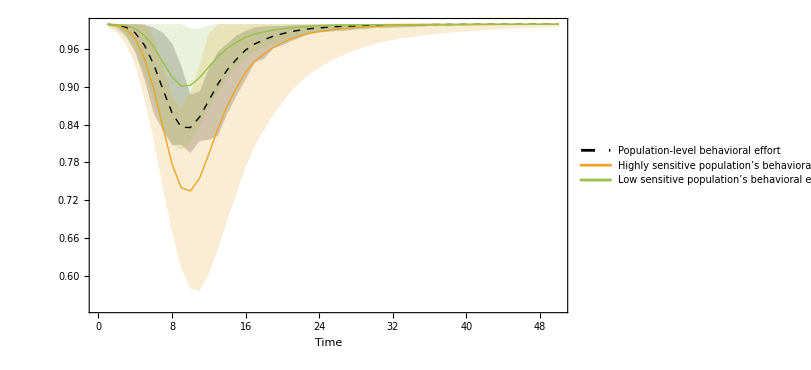

```mathematica
distplot1 = ListLinePlot[ {

{0.9998,0.9986,0.9951,0.9861,0.9666,0.9363,0.8967,0.8589,0.8359,0.8355,0.8523,0.8786,0.9051,0.9273,0.9441,0.9589,0.9686,0.9752,0.9808,0.9848,0.9883,0.9907,0.9928,0.994,0.9952,0.9962,0.9968,0.9973,0.9978,0.9983,0.9985,0.9988,0.999,0.9991,0.9992,0.9994,0.9995,0.9995,0.9996,0.9997,0.9997,0.9998,0.9998,0.9998,0.9998,0.9998,0.9999,0.9999,0.9999,0.9999},{0.9987,0.9946,0.982,0.9553,0.9123,0.859,0.8307,0.8077,0.8081,0.795,0.8141,0.8159,0.8224,0.8574,0.8857,0.9117,0.9392,0.9448,0.961,0.9664,0.9731,0.979,0.9855,0.9876,0.9882,0.9893,0.9898,0.992,0.992,0.9943,0.9943,0.9947,0.9951,0.9954,0.9963,0.9971,0.9979,0.9981,0.9981,0.9981,0.9984,0.9984,0.9986,0.9986,0.9986,0.9987,0.9989,0.999,0.999,0.999},{1.0,1.0,1.0,1.0,0.999,0.9947,0.9863,0.9696,0.9341,0.8881,0.8926,0.9287,0.9565,0.9688,0.9819,0.9893,0.9947,0.9965,0.9967,0.9971,0.9982,0.9986,0.999,0.9992,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0},{0.9997,0.9978,0.9918,0.9768,0.9451,0.8981,0.8368,0.7775,0.7397,0.7345,0.7551,0.7936,0.8344,0.8699,0.8985,0.9236,0.9408,0.9529,0.9631,0.9705,0.9773,0.9817,0.9857,0.9881,0.9904,0.9922,0.9936,0.9947,0.9958,0.9965,0.9971,0.9976,0.998,0.9982,0.9985,0.9988,0.9989,0.9991,0.9992,0.9993,0.9994,0.9995,0.9996,0.9996,0.9997,0.9997,0.9997,0.9998,0.9998,0.9998},{0.9954,0.9863,0.9674,0.9346,0.8807,0.8161,0.7404,0.6694,0.612,0.5788,0.5753,0.6016,0.6426,0.6879,0.7299,0.7726,0.806,0.8317,0.8559,0.8752,0.8943,0.9082,0.9215,0.9304,0.9394,0.9471,0.9534,0.9584,0.964,0.9683,0.9719,0.9748,0.9778,0.9792,0.9815,0.9834,0.9849,0.9861,0.9876,0.9885,0.9893,0.9905,0.9914,0.9926,0.9931,0.9934,0.9937,0.9949,0.9952,0.9957},{1.0,1.0,1.0,1.0,1.0,0.9802,0.9332,0.8856,0.8673,0.8901,0.935,0.9857,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0},{0.9999,0.9993,0.9975,0.9928,0.9821,0.964,0.9396,0.916,0.9016,0.9027,0.9151,0.9321,0.9484,0.9617,0.971,0.9792,0.9845,0.9876,0.9906,0.9927,0.9944,0.9955,0.9966,0.9972,0.9977,0.9983,0.9985,0.9988,0.999,0.9992,0.9993,0.9994,0.9995,0.9996,0.9996,0.9997,0.9998,0.9998,0.9998,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,1.0,1.0,1.0},{0.9972,0.9905,0.9784,0.9575,0.9235,0.8806,0.8375,0.8086,0.7996,0.8125,0.8374,0.8663,0.8924,0.915,0.9314,0.9463,0.9565,0.963,0.9691,0.9742,0.9783,0.9813,0.9839,0.9861,0.9877,0.9895,0.9906,0.9914,0.9922,0.9934,0.9938,0.9943,0.995,0.9954,0.9957,0.9963,0.9968,0.9969,0.9973,0.9976,0.9977,0.998,0.9981,0.9984,0.9983,0.9985,0.9985,0.9986,0.9989,0.999},{1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,0.9929,0.9929,0.9979,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0}
},
Filling->{{1->{3}},1->{2}, {4->{6}},4->{5}, , {7->{9}},7->{8}},
PlotStyle->{
Directive[Thick,Dashed,Black],None,None, 
Directive[Thick,ToColor[RGBColor["#ECA528"],Hue]],None,None, 
Directive[Thick,ToColor[RGBColor["#96C14B"],Hue]], None, None},
Frame->{True,True,False,False},
FrameLabel->{Style["Time", FontSize->22, Bold],None},
Axes->False,
LabelStyle->Directive[Bold, 24, Black],
PlotRange->{{0,50},{0.55, 1}},
ImageSize->600,
PlotLegends->Placed[{
Style["Population-level behavioral effort", FontFamily -> "Century", 20],None, None,
Style["Highly sensitive population’s behavioral effort", FontFamily -> "Century", 20], None, None,
Style["Low sensitive population’s behavioral effort", FontFamily -> "Century", 20] ,None, None}, {0.55,0.25}]];
Export["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/adaptive_networks/Figures/article_figures/subpopulations_resp_dist.pdf",distplot1,"PDF","AllowRasterization"->False];
distplot1
```

```mathematica
ctime = {1.0,1.0,1.0,1.0,1.0,1.0,1.0,0.9583,0.7917,0.4583,0.4583,0.4583,0.4583,0.4583,0.4583,0.4167,0.4167,0.375,0.3333,0.3333,0.2917,0.2917,0.2917,0.2917,0.2917,0.2917,0.3333,0.3333,0.375,0.4167,0.4167,0.4583,0.5,0.5417,0.5833,0.625,0.6667,0.7083,0.7083,0.75,0.7917,0.7917,0.8333,0.8333,0.875,0.875,0.875,0.9167,0.9167,0.9167,0.9167,0.9583,0.9583,0.9583,0.9583,0.9583,0.9583,0.9583,0.9583,0.9583,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0};
csplot=ListLinePlot[ctime,
PlotStyle->{Thick,Black, Thickness[0.008]},
TicksStyle->Directive[Bold, 12],
GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed],
PlotRange->{0,1},
PlotLegends->Placed[{
Style["Susceptible Contacts",FontFamily->"Century",11],Style["Node 469",FontFamily->"Century",11]}, {0.5,1}],
ImageSize->500];
csplot
```

-Graphics-

```mathematica
contactNetworkPlot = ListLinePlot[ {

{1.0,1.0,1.0,1.0,1.0,1.0,1.0,0.9091,0.9091,0.9091,0.8636,0.8636,0.7273,0.6364,0.5909,0.5909,0.8182,0.8182,0.7273,0.8636,0.8182,0.8182,0.9091,0.9545,0.9091,0.9091,0.9091,0.9091,0.9545,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0},{1.0,1.0,1.0,1.0,1.0,1.0,1.0,0.913,0.913,0.913,0.8696,0.8696,0.7826,0.6957,0.6957,0.6522,0.6087,0.6087,0.5652,0.5217,0.5652,0.5217,0.4783,0.4783,0.4348,0.4348,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0},{1.0,1.0,1.0,1.0,1.0,0.9375,0.9375,0.9375,0.875,0.875,0.875,0.875,0.75,0.75,0.6875,0.625,0.5625,0.625,0.5625,0.5625,0.5625,0.5,0.5,0.5,0.4375,0.4375,0.5,0.5,0.9375,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0},{1.0,1.0,1.0,1.0,1.0,1.0,1.0,0.9167,0.9167,0.9167,0.8333,0.8333,0.75,0.6667,0.6667,0.5,0.5833,0.5,0.4167,0.3333,0.5,0.5,0.5,0.5833,0.5833,0.5833,0.5833,0.5833,0.5833,0.5833,0.6667,0.75,0.75,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0},{1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,0.9333,0.8667,0.8667,0.8667,0.8,0.6667,0.6,0.6,0.6,0.6667,0.6,0.6667,0.6667,0.6667,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6667,0.6667,0.6667,0.6667,0.6667,0.8667,0.8667,0.8667,0.8667,0.8667,0.8667,0.8667,0.8667,0.8667,0.8667,0.8667,0.8667,0.8667,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0},{1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,0.9091,0.9091,0.9091,0.4091,0.5455,0.5455,0.7273,0.7273,0.8182,0.8636,0.8182,1.0,0.9091,0.9091,0.9091,0.9545,1.0,0.9545,0.9545,1.0,0.9545,0.9545,1.0,1.0,1.0,0.9545,0.9545,0.9545,1.0,0.9545,0.9545,0.9545,1.0,1.0,1.0,1.0,0.9545,0.9545,0.9545,0.9545,0.9545,0.9545,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0},{1.0,1.0,1.0,1.0,0.96,0.92,0.92,0.88,0.88,0.88,0.84,0.8,0.8,0.76,0.68,0.76,0.76,0.92,0.8,0.88,0.92,0.96,0.96,1.0,1.0,1.0,1.0,1.0,0.96,1.0,1.0,0.96,0.96,0.96,0.96,0.96,0.96,1.0,0.96,0.96,0.96,0.96,1.0,0.96,1.0,0.96,0.96,0.96,0.96,1.0,1.0,1.0,0.96,0.96,1.0,0.96,1.0,1.0,0.96,1.0,0.96,0.96,0.96,1.0,1.0,1.0,1.0,1.0,1.0,1.0},{1.0,1.0,0.9998,0.9973,0.994,0.9815,0.9538,0.9147,0.8795,0.8346,0.7841,0.7504,0.7315,0.7132,0.7256,0.7459,0.7701,0.7972,0.8302,0.8766,0.8931,0.9136,0.9313,0.9468,0.9593,0.9676,0.9798,0.9805,0.9846,0.9852,0.9898,0.9909,0.9919,0.9948,0.9958,0.996,0.996,0.996,0.996,0.9974,0.9975,0.9977,0.9977,0.9976,0.9977,0.9981,0.9981,0.9991,0.9991,0.9991,0.9991,0.9991,0.9995,0.9996,0.9995,0.9996,0.9995,0.9995,0.9996,0.9995,0.9996,0.9996,0.9996,0.9995,1.0,1.0,1.0,1.0,1.0,1.0},{1.0,1.0,0.95,0.85,0.7143,0.5625,0.5,0.3667,0.2857,0.2857,0.25,0.3077,0.2857,0.36,0.4737,0.4286,0.4286,0.4211,0.3889,0.3333,0.4286,0.4286,0.45,0.45,0.4348,0.4348,0.5,0.5,0.5263,0.5263,0.6,0.6,0.6,0.6,0.6667,0.6667,0.6667,0.6667,0.6667,0.7692,0.7692,0.7778,0.7778,0.7778,0.7778,0.7778,0.7778,0.8571,0.8571,0.8571,0.8571,0.8571,0.8571,0.8571,0.8571,0.8571,0.8571,0.8571,0.8571,0.8571,0.8571,0.8571,0.8571,0.8571,1.0,1.0,1.0,1.0,1.0,1.0},{1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0}

},
Filling->{{8->{10}},8->{9}},
PlotStyle->{ 
Directive[Thick,ToColor[RGBColor["#3366CC"],Hue]],Directive[Thick,ToColor[RGBColor["#DC3912"],Hue]],Directive[Thick,ToColor[RGBColor["#FF9900"],Hue]],Directive[Thick,ToColor[RGBColor["#109618"],Hue]],Directive[Thick,ToColor[RGBColor["#990099"],Hue]],Directive[Thick,ToColor[RGBColor["#0099C6"],Hue]],Directive[Thick,ToColor[RGBColor["#DD4477"],Hue]], 
Directive[Thick,Black, Thickness[0.008]],None,None},
Frame->{True,True,False,False},
Axes->False,
LabelStyle->Directive[Bold, Medium, Black],
PlotRange->{{0,70},{0.2, 1}},
TicksStyle->Directive[Bold, 12],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],
PlotLegends->Placed[{
Style["Node 253",FontFamily->"Century",11],Style["Node 420",FontFamily->"Century",11],Style["Node 350",FontFamily->"Century",11],Style["Node 392",FontFamily->"Century",11],Style["Node 484",FontFamily->"Century",11],Style["Node 343",FontFamily->"Century",11],Style["Node 72",FontFamily->"Century",11],
Style["Individual avg. edge reduction", FontFamily -> "Century", 11],None, None}, {0.5,1}],
ImageSize->500];
contactNetworkPlot
```

-Graphics-

```mathematica
Export["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/adaptive_networks/Figures/article_figures/csplot.pdf",csplot,"PDF","AllowRasterization"->False];
Export["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/adaptive_networks/Figures/article_figures/contactNetworkPlot.pdf",contactNetworkPlot ,"PDF","AllowRasterization"->False];
```

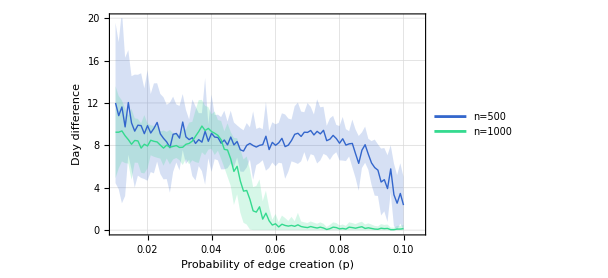

```mathematica
xsc={0.01,0.011,0.012,0.013,0.014,0.015,0.016,0.017,0.018,0.019,0.02,0.021,0.022,
0.023,0.024,0.025,0.026,0.027,0.028,0.029,0.03,0.031,0.032,0.033,0.034,0.035,
0.036,0.037,0.038,0.039,0.04,0.041,0.042,0.043,0.044,0.045,0.046,0.047,0.048,
0.049,0.05,0.051,0.052,0.053,0.054,0.055,0.056,0.057,0.058,0.059,0.06,0.061,0.062,
0.063,0.064,0.065,0.066,0.067,0.068,0.069,0.07,0.071,0.072,0.073,0.074,0.075,0.076,
0.077,0.078,0.079,0.08,0.081,0.082,0.083,0.084,0.085,0.086,0.087,0.088,0.089,0.09,
0.091,0.092,0.093,0.094,0.095,0.096,0.097,0.098,0.099,0.1};

meanc={12.0,10.8,11.62,9.74,12.04,10.12,9.34,9.9,9.86,9.1,9.86,9.16,9.6,10.16,9.08,
8.66,8.32,7.78,9.04,9.12,8.68,10.2,8.8,8.54,8.72,8.18,8.54,8.3,9.32,8.38,9.14,
8.78,8.74,8.2,8.5,8.04,8.78,8.04,8.36,7.58,7.46,8.0,8.18,7.98,7.84,8.0,8.06,
8.86,7.6,8.28,8.0,8.24,8.66,7.88,8.02,8.46,9.04,9.14,8.84,9.24,9.22,9.4,8.98,
9.32,9.08,9.42,8.44,8.58,8.94,8.64,8.2,8.62,8.02,8.14,8.18,7.22,6.3,7.54,8.06,
7.16,6.34,5.9,5.66,4.54,4.76,3.92,5.78,3.34,2.54,3.46,2.36};

lowerc={4.4353,3.86,2.5311,3.2159,7.1038,5.7185,4.0077,5.1437,4.9236,4.8226,4.654,
5.4768,5.3574,6.4602,5.3066,4.7864,4.8182,3.5312,5.4831,6.3822,5.6399,7.5581,
6.2525,6.6318,5.1057,4.6884,6.0393,5.5651,4.2918,6.7778,5.4922,6.6971,6.5847,
5.7339,5.7354,5.8365,6.295,5.9215,6.8379,5.5287,5.4991,5.9004,6.6589,4.7571,
6.1334,6.3218,6.5974,5.6086,5.8621,6.3844,6.0205,6.3604,6.2987,4.8452,5.5089,
6.4887,6.383,6.2473,6.4895,7.3604,6.4478,7.1685,7.0476,6.2933,6.5742,7.1968,
7.038,6.6203,7.0949,7.3502,6.5838,6.5608,6.515,6.9446,5.9331,4.9406,3.7187,
5.8593,6.3528,5.6981,4.2836,3.2562,3.2221,1.3893,1.7732,0.7717,3.555,0.3872,
0.0,0.6157,0.0};

upperc={19.5647,17.74,20.7089,16.2641,16.9762,14.5215,14.6723,14.6563,14.7964,
13.3774,15.066,12.8432,13.8426,13.8598,12.8534,12.5336,11.8218,12.0288,12.5969,
11.8578,11.7201,12.8419,11.3475,10.4482,12.3343,11.6716,11.0407,11.0349,14.3482,
9.9822,12.7878,10.8629,10.8953,10.6661,11.2646,10.2435,11.265,10.1585,9.8821,
9.6313,9.4209,10.0996,9.7011,11.2029,9.5466,9.6782,9.5226,12.1114,9.3379,10.1756,
9.9795,10.1196,11.0213,10.9148,10.5311,10.4313,11.697,12.0327,11.1905,11.1196,
11.9922,11.6315,10.9124,12.3467,11.5858,11.6432,9.842,10.5397,10.7851,9.9298,9.8162,
10.6792,9.525,9.3354,10.4269,9.4994,8.8813,9.2207,9.7672,8.6219,8.3964,8.5438,
8.0979,7.6907,7.7468,7.0683,8.005,6.2928,5.1912,6.3043,5.0308};


xr1000={0.01,0.011,0.012,0.013,0.014,0.015,0.016,0.017,0.018,0.019,0.02,0.021,
0.022,0.023,0.024,0.025,0.026,0.027,0.028,0.029,0.03,0.031,0.032,0.033,0.034,
0.035,0.036,0.037,0.038,0.039,0.04,0.041,0.042,0.043,0.044,0.045,0.046,0.047,
0.048,0.049,0.05,0.051,0.052,0.053,0.054,0.055,0.056,0.057,0.058,0.059,0.06,
0.061,0.062,0.063,0.064,0.065,0.066,0.067,0.068,0.069,0.07,0.071,0.072,0.073,
0.074,0.075,0.076,0.077,0.078,0.079,0.08,0.081,0.082,0.083,0.084,0.085,0.086,
0.087,0.088,0.089,0.09,0.091,0.092,0.093,0.094,0.095,0.096,0.097,0.098,0.099,
0.1};

mean1000={9.24,9.24,9.36,8.9,8.54,8.1,8.46,8.42,7.74,8.1,7.94,8.48,8.38,8.32,
8.02,7.74,8.02,7.82,7.9,7.98,7.8,7.82,8.1,8.18,8.4,8.86,9.3,9.82,9.4,9.6,
9.3,9.14,8.94,8.52,7.62,7.56,6.72,5.54,6.02,4.64,3.68,3.74,2.9,1.82,1.7,
2.2,1.04,1.6,0.88,0.48,0.6,0.3,0.56,0.44,0.38,0.44,0.36,0.5,0.34,0.28,0.24,
0.34,0.26,0.2,0.28,0.2,0.06,0.14,0.28,0.24,0.12,0.16,0.1,0.28,0.24,0.18,0.26,
0.32,0.16,0.22,0.16,0.1,0.08,0.18,0.14,0.16,0.04,0.04,0.1,0.1,0.14};

lower1000={4.8996,5.826,6.4832,6.3266,6.2793,4.7543,6.3681,6.3489,5.4117,5.3502,
5.8171,7.0623,6.9247,6.8293,6.7504,6.0763,6.7666,6.1951,6.667,6.8108,6.6048,
6.1456,6.7113,6.2141,6.5817,6.4188,6.3359,7.3482,7.0701,7.5898,7.668,7.0895,
7.4914,6.733,5.907,5.0434,4.1802,2.3764,3.3743,1.6587,0.694,0.5277,0.0626,
0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,
0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,
0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0};

upper1000={13.5804,12.654,12.2368,11.4734,10.8007,11.4457,10.5519,10.4911,
10.0683,10.8498,10.0629,9.8977,9.8353,9.8107,9.2896,9.4037,9.2734,9.4449,
9.133,9.1492,8.9952,9.4944,9.4887,10.1459,10.2183,11.3012,12.2641,12.2918,
11.7299,11.6102,10.932,11.1905,10.3886,10.307,9.333,10.0766,9.2598,8.7036,
8.6657,7.6213,6.666,6.9523,5.7374,4.0578,4.1599,4.7873,2.7298,3.7189,2.1195,
0.9847,1.5258,0.7629,1.3722,1.1445,0.8703,1.2522,0.8449,1.6294,0.8185,0.7336,
0.6714,0.8185,0.7031,0.6041,0.7336,0.6041,0.2999,0.4905,0.7336,0.6714,0.4483,
0.5303,0.403,0.7336,0.6714,0.5681,0.7031,0.7912,0.5303,0.6385,0.5303,0.403,
0.354,0.5681,0.4905,0.5303,0.2379,0.2379,0.403,0.403,0.4905};

tdb=TemporalData[{meanc,lowerc, upperc, mean1000, lower1000, upper1000},{{xsc},{xsc}, {xsc}, {xsc},{xsc}, {xsc}}];

connectivityPlot = ListLinePlot[ tdb,
Filling->{{1->{2}},{1->{3}}, {4->{6}}, {4->{5}}},
PlotStyle->{ 
Directive[Thick,ToColor[RGBColor["#3366CC"],Hue]],None,None, 
 Directive[Thick,ToColor[RGBColor["#34DA8F"],Hue]],None,None},
Frame->{True,True,False,False},
Axes->False,
FrameLabel->{Style["Probability of edge creation (p)", Black, 16 , FontFamily->"Century"], Style["Day difference", Black, 16, FontFamily->"Century"]},
LabelStyle->Directive[Bold, 18,Black],
PlotRange->{{0.01,0.105}, {-0.05,20}},
(*PlotLabel->Style[Row@{"B)",Spacer[500]}, FontSize->22, FontColor->Black, FontFamily -> "Century"],*)
TicksStyle->Directive[Bold, 12],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],
PlotLegends->Placed[{
Style["n=500",FontFamily->"Century",11],None, None, 
Style["n=1000",FontFamily->"Century",11],None, None }, {0.9,0.9}],
ImageSize->450];
(*Export["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/adaptive_networks/Figures/article_figures/connectivityPlot.pdf",connectivityPlot ,"PDF","AllowRasterization"->False];*)
connectivityPlot
```

```mathematica
plot  = GraphicsRow[{plot2, connectivityPlot }, ImageSize->1300];
Export["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/adaptive_networks/Figures/article_figures/PlotFig3A.pdf",plot2 ,"PDF","AllowRasterization"->False];
Export["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/adaptive_networks/Figures/article_figures/PlotFig3B.pdf",connectivityPlot,"PDF","AllowRasterization"->False];
plot
```

-Graphics-

```mathematica
meanconn0={0.9999,0.9998,0.9996,0.9996,0.9995,0.9995,0.9994,0.9993,0.9993,0.9993,0.9993,0.9992,0.9992,0.9992,0.9993,0.9993,0.9993,0.9993,0.9994,0.9994,0.9994,0.9994,0.9994,0.9995,0.9994,0.9994,0.9994,0.9994,0.9995,0.9994,0.9994,0.9993,0.9994,0.9994,0.9994,0.9994,0.9994,0.9994,0.9995,0.9995,0.9994,0.9995,0.9994,0.9995,0.9994,0.9994,0.9994,0.9994,0.9994,0.9994,0.9995,0.9995,0.9995,0.9995,0.9996,0.9996,0.9996,0.9996,0.9996,0.9996,0.9996,0.9996,0.9996,0.9996,0.9996,0.9996,0.9996,0.9996,0.9995,0.9995,0.9995,0.9996,0.9995,0.9995,0.9995,0.9995,0.9996,0.9995,0.9996,0.9995,0.9996,0.9996,0.9996,0.9996,0.9996,0.9996,0.9996,0.9996,0.9996,0.9996,0.9996,0.9996,0.9996,0.9996,0.9996,0.9997,0.9997,0.9997,0.9997,0.9997};

lowerconn0={0.9995,0.999,0.9986,0.9987,0.9983,0.9982,0.9982,0.9978,0.9978,0.9979,0.9978,0.9975,0.9975,0.9975,0.9976,0.9976,0.9978,0.9979,0.998,0.9979,0.998,0.998,0.998,0.9983,0.9981,0.998,0.9979,0.9977,0.9979,0.9977,0.9978,0.9978,0.9979,0.998,0.9979,0.9979,0.9978,0.9979,0.998,0.9981,0.9979,0.998,0.9978,0.9978,0.9977,0.9977,0.9978,0.9978,0.9977,0.9978,0.9978,0.9979,0.9981,0.9983,0.9985,0.9985,0.9983,0.9982,0.9981,0.9982,0.9981,0.9982,0.9983,0.9982,0.9981,0.9982,0.9982,0.998,0.9977,0.9976,0.9977,0.9979,0.9979,0.9978,0.9979,0.998,0.9981,0.9979,0.9982,0.998,0.9981,0.9982,0.9981,0.998,0.9982,0.998,0.9982,0.9981,0.9983,0.9983,0.9984,0.9983,0.9982,0.9983,0.9982,0.9984,0.9984,0.9983,0.9984,0.9986};

upperconn0={1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1};


meanconn1={0.9996,0.9989,0.9983,0.9976,0.997,0.9963,0.9956,0.995,0.9943,0.9935,0.993,0.9921,0.9915,0.9905,0.9901,0.9888,0.9875,0.9859,0.9846,0.9833,0.9821,0.9801,0.9789,0.9767,0.9739,0.9716,0.9692,0.965,0.9607,0.9572,0.9523,0.9473,0.941,0.9353,0.9276,0.9207,0.9139,0.9065,0.8999,0.8928,0.8849,0.8749,0.8652,0.8565,0.8468,0.8404,0.8363,0.83,0.8241,0.8197,0.8156,0.8109,0.8074,0.8028,0.7992,0.7955,0.7895,0.7834,0.7805,0.7803,0.7776,0.7775,0.7763,0.777,0.7777,0.7849,0.7877,0.7875,0.7906,0.7941,0.7992,0.8056,0.8097,0.8157,0.8176,0.8197,0.8222,0.8261,0.8281,0.8322,0.8382,0.8442,0.8495,0.8539,0.8598,0.8666,0.8771,0.8843,0.8908,0.8967,0.8962,0.9024,0.9128,0.9176,0.925,0.9322,0.9347,0.9386,0.9421,0.947};

lowerconn1={0.9981,0.9969,0.9955,0.9941,0.9934,0.992,0.9904,0.9889,0.9871,0.9854,0.9844,0.9819,0.9804,0.9786,0.9781,0.9749,0.9718,0.9684,0.9654,0.9637,0.9612,0.9572,0.9546,0.951,0.9462,0.9421,0.938,0.9311,0.9247,0.9195,0.9122,0.9058,0.8969,0.8899,0.8797,0.8714,0.8643,0.8563,0.8501,0.8428,0.8357,0.8261,0.817,0.8101,0.8012,0.7964,0.7948,0.7895,0.7843,0.7804,0.7772,0.7729,0.7704,0.7663,0.7625,0.7582,0.7512,0.7449,0.7426,0.7409,0.7392,0.7408,0.741,0.7441,0.7468,0.7559,0.7607,0.7623,0.7667,0.7714,0.7783,0.7864,0.7915,0.7983,0.8012,0.8042,0.8079,0.8124,0.8155,0.8211,0.8279,0.8351,0.8414,0.8467,0.8535,0.8608,0.8719,0.8796,0.8866,0.8929,0.8926,0.8989,0.9097,0.9149,0.9227,0.9304,0.933,0.937,0.9407,0.9457};

upperconn1={1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,0.9988,0.9966,0.9948,0.9925,0.9887,0.985,0.9807,0.9756,0.97,0.9635,0.9567,0.9497,0.9428,0.9342,0.9237,0.9134,0.903,0.8923,0.8844,0.8778,0.8705,0.8639,0.8591,0.854,0.8489,0.8444,0.8393,0.836,0.8329,0.8278,0.8219,0.8184,0.8196,0.8161,0.8141,0.8116,0.8099,0.8086,0.8139,0.8147,0.8127,0.8144,0.8169,0.82,0.8248,0.828,0.8332,0.834,0.8351,0.8364,0.8398,0.8406,0.8434,0.8484,0.8533,0.8576,0.8611,0.8661,0.8725,0.8823,0.889,0.895,0.9005,0.8999,0.906,0.9159,0.9202,0.9272,0.934,0.9364,0.9401,0.9435,0.9482};


meanconn2={0.9997,0.9986,0.9969,0.9943,0.9922,0.9892,0.9859,0.9823,0.9777,0.9719,0.9665,0.9595,0.9498,0.9398,0.9282,0.9144,0.9012,0.883,0.8639,0.8429,0.8229,0.8011,0.7766,0.7528,0.7287,0.7074,0.6877,0.6706,0.6565,0.6423,0.6292,0.6242,0.6223,0.6218,0.6243,0.6313,0.6383,0.6452,0.6538,0.6644,0.6752,0.6845,0.6961,0.7096,0.7197,0.7316,0.7432,0.7515,0.7697,0.7809,0.7994,0.8147,0.8172,0.8271,0.8398,0.8508,0.8552,0.8624,0.8787,0.8799,0.8859,0.8884,0.8932,0.8973,0.906,0.9051,0.9042,0.9076,0.9201,0.9189,0.9303,0.9407,0.9407,0.9353,0.9329,0.9371,0.9371,0.9502,0.9542,0.9589,0.9589,0.9641,0.9706,0.9768,0.9828,0.9828,0.9828,0.9799,0.9799,0.9869,0.9869,0.9869,0.9907,0.9907,0.9907,0.9907,0.9907,0.9907,0.9907,0.9907};

lowerconn2={0.9973,0.9958,0.9927,0.9877,0.9836,0.977,0.9707,0.9636,0.9536,0.9403,0.9318,0.9213,0.9096,0.8969,0.8821,0.8664,0.8542,0.8371,0.8204,0.8027,0.7859,0.7657,0.7413,0.7165,0.6906,0.669,0.6476,0.6289,0.6147,0.6017,0.5893,0.5861,0.5866,0.5894,0.5965,0.6079,0.6187,0.6287,0.6398,0.6526,0.6659,0.6766,0.6895,0.7042,0.7156,0.728,0.7401,0.7488,0.7677,0.7791,0.798,0.8134,0.816,0.8261,0.8389,0.8501,0.8546,0.8618,0.8782,0.8794,0.8854,0.8879,0.8928,0.897,0.9057,0.9048,0.9039,0.9073,0.9199,0.9187,0.9301,0.9406,0.9406,0.9352,0.9328,0.9369,0.9369,0.9501,0.9541,0.9588,0.9588,0.964,0.9706,0.9768,0.9827,0.9827,0.9827,0.9799,0.9799,0.9868,0.9868,0.9868,0.9907,0.9907,0.9907,0.9907,0.9907,0.9907,0.9907,0.9907};

upperconn2={1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,0.9976,0.9901,0.9827,0.9742,0.9625,0.9481,0.9289,0.9074,0.8831,0.8598,0.8365,0.812,0.7892,0.7668,0.7459,0.7278,0.7122,0.6984,0.6829,0.6692,0.6623,0.6581,0.6541,0.6521,0.6546,0.6578,0.6617,0.6678,0.6762,0.6846,0.6924,0.7026,0.7149,0.7238,0.7352,0.7462,0.7541,0.7718,0.7826,0.8008,0.816,0.8184,0.8282,0.8407,0.8515,0.8559,0.863,0.8793,0.8804,0.8864,0.8888,0.8936,0.8977,0.9063,0.9054,0.9044,0.9078,0.9204,0.9191,0.9304,0.9408,0.9408,0.9354,0.933,0.9372,0.9372,0.9503,0.9543,0.959,0.959,0.9642,0.9707,0.9769,0.9828,0.9828,0.9828,0.98,0.98,0.9869,0.9869,0.9869,0.9908,0.9908,0.9908,0.9908,0.9908,0.9908,0.9908,0.9908};


meanconn3={1.0,0.9973,0.9931,0.9875,0.9805,0.9727,0.9625,0.9505,0.9349,0.9167,0.8981,0.8747,0.8504,0.8253,0.7992,0.7689,0.7419,0.7188,0.6985,0.6823,0.6678,0.6591,0.6536,0.6442,0.6411,0.6425,0.6436,0.6507,0.6529,0.6598,0.6721,0.6834,0.6893,0.7021,0.7161,0.7213,0.7382,0.7578,0.7615,0.801,0.8226,0.8336,0.8186,0.8075,0.7988,0.7988,0.7988,0.8135,0.8319,0.8319,0.8319,0.8319,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN};

lowerconn3={0.9971,0.9914,0.9836,0.9734,0.9603,0.9467,0.9285,0.9091,0.8848,0.8597,0.8394,0.8182,0.8015,0.785,0.7647,0.7351,0.6988,0.6663,0.6432,0.6267,0.6146,0.6114,0.612,0.6081,0.6119,0.6197,0.6277,0.6393,0.6449,0.6542,0.6688,0.681,0.6879,0.7008,0.7151,0.7205,0.7376,0.7573,0.7611,0.8007,0.8223,0.8333,0.8184,0.8073,0.7986,0.7986,0.7986,0.8133,0.8318,0.8318,0.8318,0.8318,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN};

upperconn3={1.0,1.0,1.0,1.0,1.0,0.9987,0.9965,0.9919,0.9851,0.9736,0.9569,0.9313,0.8994,0.8657,0.8336,0.8026,0.785,0.7713,0.7539,0.7378,0.721,0.7069,0.6953,0.6803,0.6703,0.6654,0.6594,0.662,0.661,0.6653,0.6755,0.6857,0.6907,0.7033,0.7171,0.7221,0.7389,0.7583,0.7619,0.8014,0.8229,0.8338,0.8189,0.8077,0.7989,0.7989,0.7989,0.8136,0.832,0.832,0.832,0.832,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN};


meanconn4={0.9999,0.996,0.9901,0.9831,0.9723,0.9604,0.9438,0.9224,0.8948,0.8634,0.8287,0.799,0.7801,0.7742,0.7859,0.8088,0.8297,0.8427,0.8561,0.8541,0.8614,0.8408,0.7644,0.7788,0.7788,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN};

lowerconn4={0.9967,0.9899,0.981,0.97,0.9562,0.9385,0.9141,0.8878,0.8572,0.8277,0.7982,0.7659,0.74,0.7304,0.7423,0.7718,0.8015,0.8248,0.8473,0.8506,0.8604,0.8404,0.7642,0.7787,0.7787,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN};

upperconn4={1.0,1.0,0.9992,0.9962,0.9884,0.9822,0.9735,0.9569,0.9323,0.8991,0.8592,0.8321,0.8202,0.818,0.8296,0.8457,0.8579,0.8606,0.8648,0.8577,0.8625,0.8412,0.7647,0.779,0.779,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN};


SuscAvgEdgeRedSWPlot = ListLinePlot[ {
meanconn0,lowerconn0,upperconn0,
meanconn1,lowerconn1,upperconn1,
meanconn2,lowerconn2,upperconn2,
meanconn3,lowerconn3,upperconn3,
meanconn4,lowerconn4,upperconn4
}, Filling->{{1->{2}},{1->{3}},{4->{5}},{4->{6}},{7->{8}},{7->{9}},{10->{11}},{10->{12}},{13->{15}},{14->{15}}},
PlotStyle->{ 
Directive[Thick,Dashed,ToColor[RGBColor["#3366CC"],Hue]],None,None,
Directive[Thick,Dashed,ToColor[RGBColor["#DC3912"],Hue]],None,None,
Directive[Thick,Dashed,ToColor[RGBColor["#FF9900"],Hue]],None,None,
Directive[Thick,Dashed,ToColor[RGBColor["#109618"],Hue]],None,None,
Directive[Thick,Dashed,ToColor[RGBColor["#990099"],Hue]],None,None
},
Frame->{True,True,False,False},
Axes->False,
FrameLabel->{Style["Days", Black, 14 ]},
LabelStyle->Directive[Bold, Medium, Black],
PlotRange->{{0,101}, {0.55,1}},
TicksStyle->Directive[Bold, 12],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],
PlotLegends->Placed[{
Style["k=5",FontFamily->"Century",14],None, None, 
Style["k=15",FontFamily->"Century",14], None, None,
Style["k=25",FontFamily->"Century",14],None, None,
Style["k=35",FontFamily->"Century",14],None, None,
Style["k=45",FontFamily->"Century",14],None, None
}, {0.5,1}],
ImageSize->700
];
Export["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/adaptive_networks/Figures/article_figures/SuscAvgEdgeRedSWPlot.pdf",SuscAvgEdgeRedSWPlot,"PDF","AllowRasterization"->False];
SuscAvgEdgeRedSWPlot
```

-Graphics-

```mathematica
xsb={5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50};

meanb={8.46,8.02,7.76,6.75,7.25,6.98,6.65,6.78,6.76,6.32,6.43,6.33,5.92,5.81,5.89,6.23,6.21,6.25,6.75,6.97,6.98,7.27,7.56,7.97,8.13,7.34,7.13,6.94,6.38,5.52,4.93,4.04,3.21,2.19,1.33,1.08,0.81,0.68,0.68,0.52,0.45,0.5,0.44,0.45,0.39,0.45};

lowerb={4.2211,3.9425,4.5751,3.3734,4.7419,4.367,4.1259,4.5938,5.1387,4.5454,4.0762,4.4602,4.0469,4.4866,4.5054,4.9519,4.4791,4.1884,4.6983,5.0607,5.2804,5.5301,5.9127,6.4494,6.4868,5.6331,5.5752,5.5487,4.8309,3.2571,2.6108,1.4156,0.4309,0.0,0.0,0.0,0.0,0.0,0.0,0.0179,0.0,0.0,0.0,0.0,0.0,0.0};

upperb={12.6989,12.0975,10.9449,10.1266,9.7581,9.593,9.1741,8.9662,8.3813,8.0946,8.7838,8.1998,7.7931,7.1334,7.2746,7.5081,7.9409,8.3116,8.8017,8.8793,8.6796,9.0099,9.2073,9.4906,9.7732,9.0469,8.6848,8.3313,7.9291,7.7829,7.2492,6.6644,5.9891,4.6341,3.1835,2.6219,1.9444,1.752,1.5888,1.0221,0.95,1.3704,0.9389,1.1223,0.8802,1.2587};

xsb1={5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50};

meanb1={7.56,6.36,7.52,6.72,7.52,7.06,6.42,6.3,5.86,6.3,5.94,6.08,5.98,6.08,5.46,6.08,5.66,6.1,6.26,6.46,7.32,6.62,7.6,7.58,7.8,8.2,8.08,7.54,7.42,6.58,6.2,5.14,4.22,2.72,1.96,1.8,0.98,0.62,0.9,0.44,0.58,0.4,0.4,0.36,0.26,0.36};

lowerb1={4.1664,3.0541,4.8002,4.0778,5.3512,5.2038,4.0718,5.1706,3.8295,4.2471,4.2813,4.94,4.6025,4.9047,3.9863,4.9764,4.1266,5.0454,5.2951,4.6282,4.9601,4.7586,5.9838,5.7384,6.3714,6.3156,6.8372,5.6642,5.9901,4.7274,4.0524,2.3115,1.4404,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0};

upperb1={10.9536,9.6659,10.2398,9.3622,9.6888,8.9162,8.7682,7.4294,7.8905,8.3529,7.5987,7.22,7.3575,7.2553,6.9337,7.1836,7.1934,7.1546,7.2249,8.2918,9.6799,8.4814,9.2162,9.4216,9.2286,10.0844,9.3228,9.4158,8.8499,8.4326,8.3476,7.9685,6.9996,5.5124,4.4749,4.3071,2.7584,1.5434,2.5933,0.9414,1.3904,0.8949,0.8949,0.8449,0.7031,0.8449};

tdba=TemporalData[{meanb,lowerb, upperb, meanb1,lowerb1, upperb1},{{xsb},{xsb}, {xsb},{xsb1},{xsb1}, {xsb1}}];

BarabasiAlbertPlot = ListLinePlot[ tdba,
Filling->{{1->{2}},1->{3}, {4->{5}},4->{6}},
PlotStyle->{ 
Directive[Thick,ToColor[RGBColor["#3366CC"],Hue]],None,None,
Directive[Thick,ToColor[RGBColor["#34DA8F"],Hue]],None,None},
Frame->{True,True,False,False},
Axes->False,
FrameLabel->{Style["Number of edges to attach to existing nodes (m)", Black, 12 ], Style["Global-local max. edge reduction difference (days)", Black, 12]},
LabelStyle->Directive[Bold, Medium, Black],
PlotRange->{{4,51}, {-0.5,15}},
TicksStyle->Directive[Bold, 12],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],
PlotLegends->Placed[{
Style["n=500",FontFamily->"Century",11],None, None,
Style["n=1000",FontFamily->"Century",11],None, None}, {0.5,1}],
ImageSize->600];
Export["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/adaptive_networks/Figures/article_figures/BarabasiAlbertPlot.pdf",BarabasiAlbertPlot ,"PDF","AllowRasterization"->False];
BarabasiAlbertPlot
```

-Graphics-

```mathematica
xssw={0.001,0.0044,0.0078,0.0112,0.0147,0.0181,0.0215,0.0249,0.0283,0.0317,0.0351,0.0386,0.042,0.0454,0.0488,0.0522,0.0556,0.059,0.0624,0.0659,0.0693,0.0727,0.0761,0.0795,0.0829,0.0863,0.0898,0.0932,0.0966,0.1};

mean0={4.02,10.28,10.94,6.84,7.32,14.22,7.24,10.58,10.26,7.58,10.26,7.1,16.04,4.1,7.12,7.7,10.56,12.9,8.98,12.04,6.86,6.5,6.24,4.58,12.26,4.44,6.2,9.78,8.84,18.18};
lower0={0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0};
upper0={18.3221,34.4089,38.9184,28.3212,22.2408,46.9809,27.9593,34.5605,31.8421,28.076,36.2064,21.9534,52.182,13.7156,31.4012,30.2906,33.3198,37.159,32.983,48.6661,28.2304,21.5268,24.1372,17.0979,41.3235,15.1898,22.6267,38.161,27.5192,58.3118};

mean1={79.94,45.12,33.18,34.04,32.54,22.96,20.98,15.32,17.04,17.06,16.94,14.42,17.44,16.78,16.14,14.68,12.64,13.92,13.22,13.5,12.04,14.1,12.7,12.42,12.16,12.92,12.44,12.08,12.18,13.18};
lower1={25.4361,19.4521,16.1306,16.3108,17.7183,11.659,11.2984,6.2772,8.2989,8.945,8.1955,9.4668,9.8884,11.3391,7.6957,8.3929,7.5299,8.2349,7.2771,7.8099,6.3045,8.5112,8.524,7.4176,7.1974,8.2696,6.8406,7.2319,8.3324,9.141};
upper1={134.4439,70.7879,50.2294,51.7692,47.3617,34.261,30.6616,24.3628,25.7811,25.175,25.6845,19.3732,24.9916,22.2209,24.5843,20.9671,17.7501,19.6051,19.1629,19.1901,17.7755,19.6888,16.876,17.4224,17.1226,17.5704,18.0394,16.9281,16.0276,17.219};

mean2={53.68,20.16,20.12,17.54,13.34,15.08,14.36,13.2,13.5,11.74,10.88,12.2,12.48,11.12,11.18,10.12,10.58,11.82,10.28,10.18,9.92,10.94,10.28,10.48,11.48,10.86,10.7,10.22,9.86,10.7};
lower2={22.3148,11.3112,9.8132,9.4179,8.6687,9.5147,8.2329,8.0097,6.4862,5.7,6.776,8.3297,7.8719,7.2727,6.5744,7.167,7.3031,6.807,7.1564,6.0117,5.6829,6.5909,6.7227,7.1222,7.2362,5.5762,7.0009,7.0753,6.6977,7.1529};
upper2={85.0452,29.0088,30.4268,25.6621,18.0113,20.6453,20.4871,18.3903,20.5138,17.78,14.984,16.0703,17.0881,14.9673,15.7856,13.073,13.8569,16.833,13.4036,14.3483,14.1571,15.2891,13.8373,13.8378,15.7238,16.1438,14.3991,13.3647,13.0223,14.2471};

mean3={16.34,12.2,11.52,11.62,10.96,11.32,10.5,9.72,10.98,11.04,10.22,10.3,10.12,10.52,9.88,10.6,10.12,9.5,10.36,9.64,10.14,9.52,10.44,10.74,9.78,10.26,10.18,9.86,10.5,10.1};
lower3={7.9378,7.3681,7.6326,8.3443,7.4902,8.4243,7.1482,6.3151,8.1122,8.5908,7.53,6.8998,7.1948,7.4148,6.6183,7.5494,7.624,6.5017,7.8876,6.9013,6.8141,7.0852,8.2162,7.9861,7.5277,7.39,7.1181,7.8907,7.8255,7.2482};
upper3={24.7422,17.0319,15.4074,14.8957,14.4298,14.2157,13.8518,13.1249,13.8478,13.4892,12.91,13.7002,13.0452,13.6252,13.1417,13.6506,12.616,12.4983,12.8324,12.3787,13.4659,11.9548,12.6638,13.4939,12.0323,13.13,13.2419,11.8293,13.1745,12.9518};

mean4={5.28,5.18,3.18,3.52,3.28,3.0,2.54,2.38,2.46,2.38,2.3,2.06,2.12,1.64,2.22,2.16,1.88,1.78,1.52,1.46,1.72,1.9,1.6,1.52,1.34,1.7,1.56,1.5,1.44,1.58};
lower4={0.6773,2.1516,1.2667,1.3325,1.3736,1.3218,0.8472,0.6552,1.0572,0.691,0.8822,0.8409,0.9309,0.6146,0.8907,0.6299,0.0213,0.3907,0.4656,0.7257,0.709,0.6836,0.6524,0.5889,0.5166,0.747,0.6529,0.711,0.6534,0.5092};
upper4={9.8827,8.2084,5.0933,5.7075,5.1864,4.6782,4.2328,4.1048,3.8628,4.069,3.7178,3.2791,3.3091,2.6654,3.5493,3.6901,3.7387,3.1693,2.5744,2.1943,2.731,3.1164,2.5476,2.4511,2.1634,2.653,2.4671,2.289,2.2266,2.6508};

tdbsw=TemporalData[{mean0,lower0,upper0,mean1,lower1,upper1,mean2,lower2,upper2,mean3,lower3,upper3,mean4,lower4,upper4},{{xssw},{xssw},{xssw},{xssw},{xssw},{xssw},{xssw},{xssw},{xssw},{xssw},{xssw},{xssw},{xssw},{xssw},{xssw}}];

SmallWorldPlot = ListLinePlot[ tdbsw, Filling->{{1->{2}},{1->{3}},{4->{5}},{4->{6}},{7->{8}},{7->{9}},{10->{11}},{10->{12}},{13->{14}},{13->{15}}},
PlotRange->{{0,0.1}, {0,140}},
PlotStyle->{ 
Directive[Thick,ToColor[RGBColor["#3366CC"],Hue]],None,None,
Directive[Thick,ToColor[RGBColor["#DC3912"],Hue]],None,None,
Directive[Thick,ToColor[RGBColor["#FF9900"],Hue]],None,None,
Directive[Thick,ToColor[RGBColor["#109618"],Hue]],None,None,
Directive[Thick,ToColor[RGBColor["#990099"],Hue]],None,None
},
Frame->{True,True,False,False},
Axes->False,
FrameLabel->{Style["Probability of rewiring each edge", Black, 14 ], Style["Days", Black, 14]},
LabelStyle->Directive[Bold, Medium, Black],
PlotRange->{{4,51}, {-0.5,15}},
TicksStyle->Directive[Bold, 12],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],
PlotLegends->Placed[{
Style["k=5",FontFamily->"Century",11],None, None, 
Style["k=15",FontFamily->"Century",11], None, None,
Style["k=20",FontFamily->"Century",11],None, None,
Style["k=35",FontFamily->"Century",11],None, None,
Style["k=50",FontFamily->"Century",11],None, None
}, {0.5,1}],
ImageSize->700
];
Export["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/adaptive_networks/Figures/article_figures/SmallWorldPlot.pdf",SmallWorldPlot ,"PDF","AllowRasterization"->False];
SmallWorldPlot
```

-Graphics-

```mathematica
meanconn0={0.9999,0.9995,0.9992,0.9993,0.999,0.9989,0.9989,0.9987,0.9986,0.9986,0.9985,0.9984,0.9985,0.9984,0.9986,0.9986,0.9986,0.9987,0.9988,0.9988,0.9988,0.9989,0.9988,0.999,0.9989,0.9989,0.9988,0.9989,0.999,0.9988,0.9988,0.9987,0.9988,0.9989,0.9989,0.9989,0.9989,0.9989,0.9989,0.9989,0.9989,0.9989,0.9989,0.999,0.9989,0.9988,0.9988,0.9988,0.9989,0.9989,0.999,0.999,0.999,0.9991,0.9992,0.9992,0.9992,0.9992,0.9992,0.9992,0.9992,0.9992,0.9993,0.9992,0.9992,0.9992,0.9992,0.9991,0.9991,0.999,0.999,0.9992,0.9991,0.9991,0.9991,0.9991,0.9992,0.9991,0.9992,0.9991,0.9992,0.9992,0.9992,0.9993,0.9992,0.9992,0.9992,0.9993,0.9993,0.9993,0.9993,0.9993,0.9993,0.9993,0.9993,0.9994,0.9994,0.9994,0.9995,0.9995};

lowerconn0={0.9995,0.9988,0.9982,0.9983,0.9978,0.9977,0.9977,0.9972,0.9972,0.9972,0.9971,0.9967,0.9968,0.9968,0.9969,0.9969,0.9971,0.9973,0.9975,0.9973,0.9974,0.9974,0.9974,0.9978,0.9976,0.9975,0.9974,0.9972,0.9974,0.9972,0.9972,0.9972,0.9974,0.9975,0.9974,0.9973,0.9973,0.9974,0.9975,0.9976,0.9974,0.9974,0.9973,0.9973,0.9972,0.9971,0.9972,0.9972,0.9972,0.9973,0.9973,0.9975,0.9976,0.9979,0.9981,0.9981,0.9979,0.9978,0.9977,0.9978,0.9978,0.9978,0.998,0.9978,0.9977,0.9978,0.9978,0.9975,0.9973,0.9971,0.9973,0.9975,0.9975,0.9974,0.9975,0.9976,0.9977,0.9975,0.9978,0.9976,0.9978,0.9979,0.9977,0.9977,0.9978,0.9977,0.9978,0.9978,0.998,0.998,0.9981,0.998,0.9978,0.998,0.9979,0.9981,0.9981,0.9981,0.9981,0.9983};

upperconn0={1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0};

meanconn0S={0.9999,0.9998,0.9996,0.9996,0.9995,0.9995,0.9994,0.9993,0.9993,0.9993,0.9993,0.9992,0.9992,0.9992,0.9993,0.9993,0.9993,0.9993,0.9994,0.9994,0.9994,0.9994,0.9994,0.9995,0.9994,0.9994,0.9994,0.9994,0.9995,0.9994,0.9994,0.9993,0.9994,0.9994,0.9994,0.9994,0.9994,0.9994,0.9995,0.9995,0.9994,0.9995,0.9994,0.9995,0.9994,0.9994,0.9994,0.9994,0.9994,0.9994,0.9995,0.9995,0.9995,0.9995,0.9996,0.9996,0.9996,0.9996,0.9996,0.9996,0.9996,0.9996,0.9996,0.9996,0.9996,0.9996,0.9996,0.9996,0.9995,0.9995,0.9995,0.9996,0.9995,0.9995,0.9995,0.9995,0.9996,0.9995,0.9996,0.9995,0.9996,0.9996,0.9996,0.9996,0.9996,0.9996,0.9996,0.9996,0.9996,0.9996,0.9996,0.9996,0.9996,0.9996,0.9996,0.9997,0.9997,0.9997,0.9997,0.9997};

lowerconn0S={0.9995,0.999,0.9986,0.9987,0.9983,0.9982,0.9982,0.9978,0.9978,0.9979,0.9978,0.9975,0.9975,0.9975,0.9976,0.9976,0.9978,0.9979,0.998,0.9979,0.998,0.998,0.998,0.9983,0.9981,0.998,0.9979,0.9977,0.9979,0.9977,0.9978,0.9978,0.9979,0.998,0.9979,0.9979,0.9978,0.9979,0.998,0.9981,0.9979,0.998,0.9978,0.9978,0.9977,0.9977,0.9978,0.9978,0.9977,0.9978,0.9978,0.9979,0.9981,0.9983,0.9985,0.9985,0.9983,0.9982,0.9981,0.9982,0.9981,0.9982,0.9983,0.9982,0.9981,0.9982,0.9982,0.998,0.9977,0.9976,0.9977,0.9979,0.9979,0.9978,0.9979,0.998,0.9981,0.9979,0.9982,0.998,0.9981,0.9982,0.9981,0.998,0.9982,0.998,0.9982,0.9981,0.9983,0.9983,0.9984,0.9983,0.9982,0.9983,0.9982,0.9984,0.9984,0.9983,0.9984,0.9986};

upperconn0S={1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1};

SuscAvgEdgeRedSWPlotK5 = ListLinePlot[ {
meanconn0,lowerconn0,upperconn0,
meanconn0S,lowerconn0S,upperconn0S
}, Filling->{{1->{2}},{1->{3}}, {4->{6}},{4->{5}}},
PlotStyle->{ 
Directive[Thick,Dashed,Black],None,None,
Directive[Thick,Dashed,Blue],None,None
},
Frame->{True,True,False,False},
Axes->False,
FrameLabel->{Style["Days", Black, 14 ]},
LabelStyle->Directive[Bold, Medium, Black],
PlotRange->{{0,101}, {0.995,1}},
TicksStyle->Directive[Bold, 12],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],
PlotLegends->Placed[{
Style["Avg. network edge reduction",FontFamily->"Century",14],None, None, 
Style["Avg. individual edge reduction",FontFamily->"Century",14], None, None
}, {0.5,1}],
ImageSize->700
];
Export["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/adaptive_networks/Figures/article_figures/SuscAvgEdgeRedSWPlotK5.pdf",SuscAvgEdgeRedSWPlotK5,"PDF","AllowRasterization"->False];
SuscAvgEdgeRedSWPlotK5
```

-Graphics-

```mathematica
imean0={0.0022,0.0028,0.003,0.0033,0.0038,0.0041,0.0042,0.0047,0.0049,0.0053,0.0054,0.0057,0.0056,0.0058,0.0056,0.0057,0.0058,0.0061,0.006,0.0061,0.0062,0.0066,0.0069,0.0067,0.0068,0.007,0.0071,0.0068,0.0068,0.0071,0.007,0.0072,0.0074,0.0072,0.0073,0.0074,0.0074,0.0077,0.0077,0.0078,0.0079,0.0079,0.008,0.008,0.0082,0.0083,0.0083,0.0082,0.0079,0.008,0.0077,0.0077,0.0078,0.0076,0.0075,0.0073,0.0073,0.0072,0.0072,0.0072,0.0072,0.0072,0.007,0.0071,0.0072,0.0073,0.0073,0.0074,0.0075,0.0078,0.0078,0.0073,0.0072,0.0073,0.0074,0.0074,0.0074,0.0074,0.0074,0.0074,0.0072,0.0072,0.0071,0.0071,0.0072,0.0071,0.0068,0.0066,0.0065,0.0065,0.0062,0.0061,0.0062,0.0059,0.0057,0.0056,0.0054,0.0052,0.0052,0.0052,0.0052,0.0053,0.0051,0.0052,0.0052,0.0054,0.0054,0.0053,0.0051,0.005,0.005,0.0049,0.0049,0.005,0.005,0.0049,0.005,0.0047,0.0046,0.0045,0.0043,0.0043,0.0042,0.0042,0.0042,0.0041,0.004,0.0038,0.0037,0.0038,0.0036,0.0036,0.0038,0.0038,0.0038,0.0036,0.0034,0.0033,0.0032,0.0032,0.0031,0.0029,0.003,0.0028,0.0028,0.0028,0.0028,0.0028,0.0028,0.0027,0.0027,0.0026,0.0026,0.0026,0.0024,0.0024,0.0023,0.0022,0.0022,0.0021,0.0021,0.0021,0.0021,0.0021,0.0022,0.0023,0.0023,0.0022,0.0022,0.0022,0.0022,0.0022,0.0021,0.0021,0.0022,0.0023,0.0022,0.0021,0.0022,0.0021,0.002,0.0018,0.0017,0.0017,0.0017,0.0015,0.0015,0.0013,0.0013,0.0012,0.0013,0.0013,0.0013,0.0013,0.0013,0.0013,0.0013,0.0014,0.0013,0.0014};

ilower0={0.0016,0.0013,0.0012,0.0012,0.0013,0.0011,0.0011,0.0012,0.0015,0.0015,0.0014,0.0015,0.001,0.0013,0.0011,0.0011,0.0014,0.0013,0.0011,0.0014,0.0016,0.0017,0.0019,0.0019,0.0015,0.0014,0.0016,0.0013,0.0011,0.0012,0.0012,0.0013,0.0011,0.0008,0.0005,0.0007,0.0008,0.0009,0.0008,0.0006,0.0003,0.0003,0.0001,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0};

iupper0={0.0029,0.0042,0.0049,0.0054,0.0063,0.0071,0.0073,0.0082,0.0084,0.0091,0.0095,0.0099,0.0102,0.0102,0.0101,0.0103,0.0103,0.0108,0.0108,0.0108,0.0108,0.0115,0.0118,0.0115,0.0121,0.0125,0.0126,0.0124,0.0124,0.0129,0.0129,0.0131,0.0137,0.0136,0.0142,0.014,0.014,0.0145,0.0146,0.0149,0.0155,0.0155,0.0159,0.0161,0.0167,0.0168,0.0166,0.0167,0.0163,0.0162,0.0159,0.0156,0.0159,0.0157,0.0155,0.0151,0.0153,0.0156,0.0154,0.0156,0.0158,0.0155,0.0152,0.0154,0.0155,0.0158,0.0157,0.0162,0.0167,0.0174,0.0176,0.0162,0.0161,0.0163,0.0168,0.017,0.0167,0.0168,0.0163,0.0161,0.0159,0.0155,0.0156,0.016,0.016,0.0162,0.0153,0.0151,0.0149,0.0149,0.0142,0.0144,0.0148,0.0139,0.0135,0.0133,0.0129,0.0127,0.013,0.0133,0.0132,0.0136,0.0133,0.0134,0.0138,0.0137,0.0141,0.014,0.0137,0.0136,0.0136,0.0135,0.0135,0.014,0.014,0.0137,0.0139,0.0135,0.0135,0.0132,0.0124,0.0122,0.0117,0.0118,0.0116,0.0115,0.011,0.0107,0.0106,0.0107,0.0102,0.0103,0.0105,0.0105,0.0106,0.0106,0.0102,0.0097,0.0097,0.0097,0.0091,0.0089,0.0091,0.0088,0.0087,0.0087,0.0086,0.0086,0.0083,0.0081,0.0084,0.0083,0.0079,0.0079,0.0074,0.0075,0.0068,0.0067,0.0067,0.0065,0.0064,0.0066,0.0066,0.0066,0.0069,0.0074,0.0074,0.0073,0.0074,0.0075,0.0073,0.0075,0.0071,0.0072,0.0073,0.0077,0.0075,0.0073,0.0075,0.0074,0.0071,0.0062,0.0058,0.006,0.0059,0.0053,0.0052,0.0046,0.0045,0.0043,0.0047,0.0049,0.005,0.0049,0.0048,0.005,0.0051,0.0054,0.005,0.0053};

InfectedSWPlotK5 = ListLinePlot[ {
imean0,ilower0,iupper0
}, Filling->{{1->{2}},{1->{3}}},
PlotStyle->{ 
Directive[Thick,Dashed,Red],None,None
},
Frame->{True,True,False,False},
Axes->False,
FrameLabel->{Style["Days", Black, 14 ]},
LabelStyle->Directive[Bold, Medium, Black],
PlotRange->{{0,201}, {0,0.018}},
TicksStyle->Directive[Bold, 12],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],
PlotLegends->Placed[{
Style["Infected population",FontFamily->"Century",14],None, None
}, {0.5,1}],
ImageSize->700
];
Export["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/adaptive_networks/Figures/article_figures/InfectedSWPlotK5.pdf",InfectedSWPlotK5,"PDF","AllowRasterization"->False];
InfectedSWPlotK5
```

-Graphics-

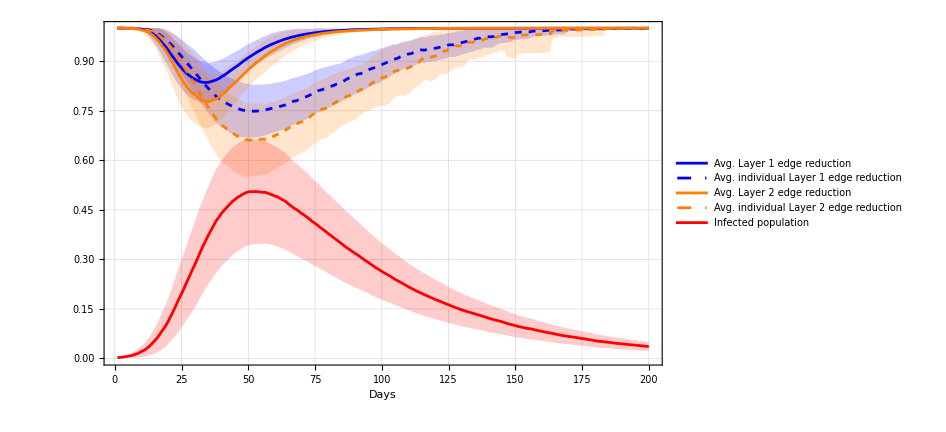

```mathematica
mean1={1.0,1.0,1.0,1.0,0.9999,0.9999,0.9996,0.9992,0.9985,0.9972,0.996,0.9933,0.9897,0.9847,0.9784,0.9719,0.9629,0.9532,0.9443,0.9335,0.9217,0.9109,0.8996,0.889,0.8801,0.8706,0.8625,0.8562,0.8501,0.8456,0.8413,0.838,0.8361,0.8356,0.836,0.8384,0.8408,0.8435,0.8477,0.8531,0.858,0.8635,0.8696,0.8754,0.8812,0.8866,0.8929,0.8992,0.9052,0.9107,0.9159,0.921,0.9263,0.931,0.9355,0.9404,0.9445,0.9486,0.952,0.9552,0.9587,0.9617,0.9648,0.9676,0.9699,0.9724,0.9742,0.9762,0.9781,0.9796,0.9811,0.9827,0.9838,0.985,0.9861,0.9872,0.9881,0.9891,0.99,0.9906,0.9912,0.9919,0.9924,0.993,0.9933,0.9938,0.9942,0.9947,0.995,0.9954,0.9957,0.996,0.9963,0.9964,0.9967,0.9969,0.9971,0.9972,0.9975,0.9976,0.9978,0.998,0.9982,0.9983,0.9984,0.9985,0.9986,0.9987,0.9988,0.9988,0.9989,0.999,0.999,0.9991,0.9992,0.9992,0.9993,0.9993,0.9993,0.9994,0.9994,0.9995,0.9995,0.9996,0.9996,0.9996,0.9996,0.9997,0.9997,0.9997,0.9997,0.9997,0.9998,0.9998,0.9998,0.9998,0.9998,0.9998,0.9998,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0};
lower1={1.0,0.9999,0.9999,0.9999,0.9997,0.9996,0.9988,0.9974,0.9957,0.9923,0.99,0.9836,0.9756,0.9645,0.9528,0.9419,0.9272,0.9116,0.8987,0.8836,0.8671,0.8536,0.8395,0.8271,0.8168,0.8066,0.7984,0.7915,0.785,0.7814,0.7782,0.776,0.775,0.7754,0.7771,0.7809,0.7842,0.7878,0.793,0.8002,0.8065,0.8134,0.8206,0.8275,0.8352,0.8415,0.8492,0.8563,0.8633,0.8699,0.8763,0.8823,0.8887,0.8946,0.8994,0.9057,0.9106,0.915,0.9189,0.9234,0.9278,0.932,0.9362,0.9406,0.9445,0.9484,0.9516,0.9547,0.9581,0.9611,0.9636,0.9668,0.9695,0.9716,0.9733,0.9752,0.9768,0.9788,0.9807,0.9821,0.9831,0.9847,0.9861,0.9873,0.9879,0.9888,0.9895,0.9904,0.9908,0.9915,0.9921,0.9925,0.9932,0.9935,0.9938,0.9943,0.9947,0.9949,0.9953,0.9957,0.9962,0.9965,0.9967,0.997,0.9972,0.9973,0.9974,0.9976,0.9977,0.9978,0.9979,0.998,0.9981,0.9982,0.9983,0.9984,0.9985,0.9986,0.9986,0.9987,0.9988,0.999,0.9991,0.9991,0.9992,0.9992,0.9992,0.9993,0.9993,0.9993,0.9993,0.9994,0.9994,0.9994,0.9995,0.9995,0.9995,0.9996,0.9996,0.9996,0.9996,0.9996,0.9997,0.9997,0.9997,0.9997,0.9997,0.9997,0.9997,0.9998,0.9998,0.9998,0.9998,0.9998,0.9998,0.9998,0.9998,0.9998,0.9998,0.9998,0.9998,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0};
upper1={1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,0.9986,0.9947,0.99,0.9835,0.9763,0.9682,0.9598,0.951,0.9433,0.9345,0.9266,0.9209,0.9151,0.9097,0.9044,0.9001,0.8972,0.8958,0.8949,0.8959,0.8975,0.8993,0.9025,0.906,0.9095,0.9136,0.9187,0.9232,0.9273,0.9317,0.9366,0.9422,0.9471,0.9515,0.9555,0.9598,0.964,0.9675,0.9716,0.9752,0.9784,0.9823,0.9851,0.9869,0.9895,0.9914,0.9934,0.9945,0.9954,0.9965,0.9969,0.9977,0.9981,0.9981,0.9986,0.9985,0.9981,0.9984,0.9989,0.9993,0.9994,0.9994,0.9994,0.9991,0.9992,0.9991,0.9988,0.9986,0.9987,0.9987,0.9989,0.9991,0.9992,0.9992,0.9994,0.9995,0.9994,0.9994,0.9996,0.9995,0.9995,0.9996,0.9996,0.9996,0.9995,0.9996,0.9996,0.9997,0.9997,0.9998,0.9998,0.9999,0.9999,0.9999,0.9999,0.9999,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0};

suscmean1={1.0,1.0,1.0,1.0,1.0,0.9999,0.9998,0.9996,0.9993,0.9986,0.998,0.9966,0.9946,0.9919,0.9883,0.9845,0.979,0.9729,0.9671,0.9598,0.9512,0.9426,0.9332,0.9237,0.9148,0.9047,0.8949,0.8857,0.8755,0.8664,0.8562,0.8459,0.8362,0.8271,0.8178,0.8102,0.8018,0.7933,0.7875,0.7818,0.7769,0.7721,0.7677,0.7636,0.7598,0.7563,0.754,0.7518,0.7507,0.749,0.7488,0.7487,0.749,0.7496,0.7517,0.7516,0.7537,0.7558,0.7581,0.76,0.7612,0.7634,0.7657,0.7678,0.7718,0.7761,0.7789,0.7802,0.7838,0.7862,0.7904,0.7935,0.7971,0.8014,0.806,0.8102,0.8125,0.8149,0.819,0.8213,0.824,0.8268,0.8306,0.8329,0.8371,0.8411,0.8465,0.85,0.8538,0.857,0.8613,0.8623,0.8656,0.8696,0.8738,0.8772,0.88,0.8824,0.885,0.8896,0.8933,0.8965,0.9002,0.9048,0.9069,0.9092,0.9138,0.9178,0.9191,0.9221,0.9229,0.927,0.9294,0.9324,0.9346,0.9332,0.9361,0.9373,0.9384,0.9394,0.9408,0.9431,0.9435,0.946,0.9493,0.9498,0.9499,0.9519,0.9549,0.9565,0.9584,0.9606,0.9629,0.964,0.9672,0.9694,0.9702,0.974,0.9739,0.974,0.974,0.975,0.979,0.9802,0.981,0.9818,0.9828,0.9831,0.9859,0.9868,0.9873,0.9881,0.9884,0.9884,0.9884,0.9899,0.9916,0.9916,0.9916,0.9919,0.9924,0.9936,0.9936,0.9933,0.9942,0.9947,0.9947,0.9945,0.996,0.9979,0.9978,0.9978,0.9978,0.9978,0.9978,0.9986,0.9986,0.9986,0.9986,0.9986,0.9986,0.9986,0.9995,0.9995,0.9995,0.9995,0.9995,0.9995,0.9995,0.9995,0.9995,0.9995,0.9995,0.9995,0.9995,0.9994,0.9994,0.9994,0.9994,0.9994};
susclower1={1.0,1.0,0.9999,0.9999,0.9999,0.9998,0.9994,0.9987,0.9979,0.9961,0.9949,0.9915,0.9871,0.9807,0.9737,0.9669,0.9577,0.9475,0.9385,0.9275,0.9144,0.9021,0.8888,0.8757,0.8634,0.8505,0.8377,0.825,0.8115,0.7998,0.787,0.7744,0.7631,0.7524,0.7412,0.7322,0.7225,0.7123,0.706,0.6997,0.6945,0.6893,0.6844,0.6806,0.6768,0.6732,0.671,0.6695,0.6691,0.6677,0.6684,0.6687,0.6692,0.6705,0.6739,0.6741,0.6771,0.6802,0.6832,0.6855,0.687,0.6899,0.6925,0.6948,0.6998,0.7047,0.7083,0.7096,0.7139,0.7165,0.7219,0.7257,0.7301,0.7347,0.7399,0.7453,0.7477,0.7503,0.7559,0.7588,0.7619,0.7656,0.77,0.7737,0.7785,0.7832,0.7878,0.7918,0.7963,0.8,0.8054,0.8065,0.811,0.8156,0.8211,0.8253,0.8286,0.8322,0.8326,0.8398,0.8439,0.848,0.8536,0.8591,0.8629,0.866,0.8707,0.8764,0.8781,0.8818,0.8822,0.8862,0.89,0.8925,0.8966,0.8943,0.8985,0.8977,0.8998,0.9006,0.9028,0.9046,0.9063,0.9089,0.9131,0.9131,0.9126,0.9143,0.9179,0.9213,0.9226,0.9257,0.9277,0.9285,0.9324,0.9346,0.936,0.9408,0.9413,0.9409,0.9409,0.9427,0.9504,0.9536,0.9548,0.9556,0.9564,0.9573,0.9623,0.9647,0.9651,0.9668,0.9671,0.9671,0.9671,0.9727,0.9758,0.9758,0.9758,0.9764,0.977,0.9794,0.9794,0.979,0.9802,0.9816,0.9816,0.9812,0.9848,0.9918,0.9916,0.9916,0.9916,0.9916,0.9916,0.9935,0.9935,0.9935,0.9935,0.9935,0.9935,0.9935,0.997,0.997,0.997,0.997,0.997,0.997,0.997,0.997,0.997,0.997,0.997,0.9969,0.9969,0.9968,0.9968,0.9968,0.9968,0.9968};
suscupper1={1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,0.9984,0.9958,0.9921,0.988,0.9831,0.9777,0.9717,0.9661,0.959,0.9521,0.9463,0.9396,0.933,0.9253,0.9175,0.9094,0.9017,0.8944,0.8882,0.8812,0.8744,0.8689,0.8638,0.8593,0.8549,0.8511,0.8467,0.8428,0.8394,0.837,0.8341,0.8323,0.8304,0.8292,0.8286,0.8288,0.8287,0.8296,0.8292,0.8302,0.8314,0.8329,0.8346,0.8354,0.8369,0.8388,0.8407,0.8438,0.8475,0.8495,0.8508,0.8537,0.8559,0.859,0.8612,0.8642,0.8681,0.8722,0.8752,0.8774,0.8794,0.8822,0.8839,0.886,0.888,0.8912,0.8921,0.8956,0.899,0.9051,0.9082,0.9112,0.914,0.9172,0.918,0.9201,0.9235,0.9266,0.929,0.9314,0.9327,0.9375,0.9395,0.9426,0.945,0.9467,0.9505,0.951,0.9524,0.9569,0.9592,0.9601,0.9624,0.9635,0.9677,0.9688,0.9723,0.9726,0.9721,0.9737,0.9769,0.977,0.9783,0.9788,0.9815,0.9807,0.9831,0.9854,0.9865,0.9872,0.9896,0.9918,0.9918,0.9942,0.9955,0.9981,0.9995,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0};

mean2={1.0,1.0,0.9999,0.9997,0.9996,0.9992,0.9984,0.9979,0.9966,0.9945,0.9928,0.9895,0.9849,0.9794,0.9725,0.9645,0.9543,0.9432,0.933,0.9197,0.9042,0.8906,0.8743,0.8594,0.8471,0.834,0.8228,0.813,0.8039,0.798,0.7909,0.7855,0.7809,0.7788,0.7781,0.7802,0.7831,0.7861,0.7909,0.7973,0.804,0.8115,0.8204,0.8277,0.835,0.8424,0.8506,0.8586,0.8664,0.8744,0.8818,0.8889,0.896,0.9021,0.9081,0.915,0.9203,0.9266,0.9314,0.9361,0.9413,0.9457,0.95,0.9541,0.9573,0.9606,0.9635,0.9663,0.9689,0.971,0.973,0.9754,0.9771,0.9789,0.9802,0.9817,0.9829,0.9843,0.9854,0.9863,0.9874,0.9884,0.9892,0.99,0.9904,0.9909,0.9915,0.9922,0.9925,0.993,0.9935,0.9939,0.9943,0.9946,0.9949,0.9954,0.9957,0.9959,0.9963,0.9965,0.9968,0.997,0.9972,0.9974,0.9976,0.9977,0.9978,0.9979,0.998,0.998,0.9981,0.9982,0.9984,0.9985,0.9986,0.9987,0.9988,0.9989,0.999,0.999,0.9991,0.9992,0.9993,0.9993,0.9994,0.9994,0.9995,0.9995,0.9995,0.9995,0.9995,0.9996,0.9996,0.9996,0.9997,0.9997,0.9997,0.9997,0.9998,0.9998,0.9998,0.9998,0.9998,0.9998,0.9998,0.9998,0.9998,0.9998,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0};
lower2={0.9999,0.9998,0.9996,0.9993,0.9989,0.9979,0.9958,0.9945,0.992,0.9868,0.9837,0.9764,0.9669,0.9555,0.9426,0.9294,0.9123,0.8937,0.8782,0.8589,0.8361,0.8175,0.7967,0.7778,0.7635,0.7488,0.7371,0.7264,0.7164,0.7118,0.7059,0.7026,0.6991,0.6978,0.6981,0.7017,0.7061,0.7102,0.7163,0.725,0.7341,0.7436,0.7548,0.7642,0.7734,0.7827,0.7929,0.8018,0.8108,0.82,0.8295,0.8375,0.8459,0.8524,0.8588,0.8664,0.8725,0.88,0.886,0.8924,0.8993,0.9052,0.9112,0.918,0.9229,0.9273,0.9326,0.9369,0.9416,0.9453,0.9489,0.9531,0.9567,0.96,0.9619,0.9646,0.9668,0.9692,0.9716,0.9737,0.9755,0.978,0.9801,0.9817,0.9824,0.9835,0.9846,0.9855,0.9862,0.9869,0.9879,0.9886,0.9895,0.99,0.9906,0.9914,0.9921,0.9924,0.9931,0.9936,0.9941,0.9944,0.9949,0.9952,0.9954,0.9955,0.9958,0.996,0.9961,0.9963,0.9964,0.9965,0.9967,0.9968,0.9971,0.9974,0.9975,0.9976,0.9977,0.9978,0.998,0.9983,0.9984,0.9984,0.9986,0.9987,0.9988,0.9988,0.9988,0.9988,0.9989,0.9991,0.9991,0.9991,0.9992,0.9993,0.9993,0.9993,0.9994,0.9994,0.9994,0.9995,0.9995,0.9995,0.9995,0.9995,0.9995,0.9995,0.9996,0.9996,0.9997,0.9997,0.9997,0.9997,0.9997,0.9997,0.9998,0.9998,0.9998,0.9998,0.9998,0.9998,0.9998,0.9998,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0};
upper2={1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,0.9996,0.9963,0.9926,0.9879,0.9806,0.9723,0.9636,0.9519,0.9409,0.9308,0.9192,0.9085,0.8996,0.8914,0.8842,0.8759,0.8683,0.8627,0.8598,0.8581,0.8587,0.8602,0.862,0.8655,0.8696,0.8739,0.8794,0.8861,0.8912,0.8966,0.9021,0.9083,0.9154,0.922,0.9288,0.9342,0.9402,0.946,0.9519,0.9575,0.9636,0.9681,0.9732,0.9768,0.9798,0.9834,0.9861,0.9888,0.9903,0.9917,0.9939,0.9944,0.9957,0.9962,0.9966,0.9972,0.9976,0.9976,0.9978,0.9986,0.9989,0.999,0.9994,0.9992,0.9989,0.9992,0.9988,0.9983,0.9983,0.9984,0.9984,0.9985,0.9989,0.9989,0.999,0.9991,0.9993,0.9991,0.9992,0.9993,0.9993,0.9993,0.9994,0.9994,0.9993,0.9995,0.9995,0.9996,0.9997,0.9998,0.9998,0.9998,0.9998,0.9998,0.9998,0.9999,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0};

suscmean2={1.0,1.0,0.9999,0.9999,0.9998,0.9996,0.9992,0.999,0.9984,0.9974,0.9966,0.9949,0.9926,0.9896,0.9858,0.9813,0.9753,0.9687,0.9624,0.9537,0.9428,0.9323,0.9196,0.9067,0.895,0.8815,0.8686,0.8557,0.8417,0.83,0.8154,0.801,0.7867,0.7738,0.7608,0.749,0.7377,0.7254,0.7161,0.7079,0.7013,0.6954,0.6907,0.6833,0.6779,0.6729,0.6698,0.6654,0.6629,0.661,0.6614,0.6614,0.662,0.6628,0.6639,0.6637,0.664,0.6694,0.6716,0.6748,0.6786,0.6841,0.6868,0.692,0.697,0.7026,0.7074,0.709,0.7141,0.7163,0.7202,0.7245,0.731,0.7381,0.7432,0.7487,0.752,0.7559,0.757,0.7617,0.7704,0.7722,0.7766,0.782,0.7871,0.7893,0.7943,0.796,0.8009,0.8023,0.8086,0.8135,0.8169,0.8236,0.825,0.8326,0.8368,0.8425,0.8451,0.8501,0.8512,0.8553,0.8589,0.8653,0.8712,0.8723,0.8756,0.8754,0.8762,0.8804,0.8837,0.8914,0.895,0.8983,0.9059,0.9104,0.9119,0.9109,0.9142,0.9151,0.9202,0.9267,0.9305,0.9306,0.9374,0.939,0.943,0.9471,0.9458,0.9469,0.9501,0.9559,0.9579,0.9579,0.958,0.9593,0.9616,0.965,0.9685,0.9684,0.9716,0.9734,0.9726,0.9763,0.9763,0.9763,0.9726,0.9726,0.9711,0.9718,0.9766,0.9774,0.9789,0.9796,0.9796,0.9796,0.9802,0.9802,0.9802,0.9812,0.9809,0.9826,0.9826,0.9922,0.9928,0.9928,0.9944,0.9942,0.994,0.994,0.9938,0.9947,0.9947,0.9947,0.9947,0.9947,0.9947,0.996,0.996,0.996,0.996,0.996,0.996,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0};
susclower2={1.0,0.9999,0.9998,0.9997,0.9995,0.9991,0.998,0.9974,0.9962,0.9937,0.9922,0.9883,0.9833,0.9768,0.9694,0.9615,0.951,0.9394,0.9291,0.9156,0.898,0.8818,0.8635,0.8448,0.8285,0.8103,0.793,0.7754,0.7564,0.7416,0.7232,0.7067,0.691,0.6754,0.6595,0.645,0.6317,0.6165,0.6058,0.5969,0.5896,0.5832,0.5783,0.5698,0.5644,0.5589,0.5564,0.5527,0.5505,0.5495,0.5509,0.5516,0.5521,0.5541,0.5561,0.5563,0.5569,0.5641,0.5677,0.5719,0.5762,0.5829,0.5863,0.5926,0.5989,0.6059,0.6118,0.6132,0.6184,0.621,0.6258,0.6308,0.6384,0.6456,0.6511,0.6587,0.6618,0.6673,0.6677,0.6716,0.6828,0.6839,0.6906,0.6978,0.7046,0.7072,0.7122,0.7139,0.7206,0.7221,0.7307,0.7373,0.7427,0.7488,0.7476,0.7544,0.758,0.7626,0.7614,0.7679,0.7635,0.7702,0.7714,0.7832,0.7927,0.795,0.7973,0.7963,0.7958,0.8033,0.8069,0.8194,0.8216,0.8259,0.8348,0.8421,0.844,0.8386,0.8418,0.8419,0.8526,0.8584,0.8636,0.8582,0.8675,0.8702,0.8746,0.8825,0.881,0.8834,0.8867,0.8986,0.9051,0.9051,0.9055,0.9081,0.9116,0.9149,0.9186,0.9188,0.9218,0.9265,0.9253,0.932,0.932,0.932,0.9122,0.9122,0.9084,0.9091,0.9219,0.9225,0.9238,0.9246,0.9246,0.9246,0.9243,0.9243,0.9243,0.9253,0.9248,0.9269,0.9269,0.9708,0.9715,0.9715,0.9745,0.9739,0.9734,0.9734,0.9727,0.9739,0.9739,0.9739,0.9739,0.9739,0.9739,0.976,0.976,0.976,0.976,0.976,0.976,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0};
suscupper2={1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,0.9996,0.9981,0.9958,0.9918,0.9875,0.9828,0.9756,0.9686,0.9615,0.9528,0.9442,0.9359,0.9269,0.9184,0.9076,0.8953,0.8825,0.8721,0.8621,0.853,0.8438,0.8343,0.8263,0.819,0.8129,0.8077,0.803,0.7967,0.7914,0.787,0.7832,0.7781,0.7752,0.7724,0.772,0.7712,0.7718,0.7715,0.7717,0.771,0.7711,0.7746,0.7755,0.7777,0.781,0.7853,0.7874,0.7914,0.7951,0.7993,0.803,0.8048,0.8098,0.8117,0.8145,0.8182,0.8237,0.8305,0.8353,0.8386,0.8422,0.8444,0.8464,0.8519,0.858,0.8605,0.8625,0.8661,0.8695,0.8714,0.8764,0.8782,0.8812,0.8825,0.8864,0.8896,0.8911,0.8985,0.9024,0.9108,0.9156,0.9224,0.9288,0.9323,0.9389,0.9404,0.9463,0.9474,0.9498,0.9496,0.9538,0.9545,0.9566,0.9575,0.9606,0.9635,0.9683,0.9708,0.977,0.9786,0.9799,0.9831,0.9867,0.9883,0.9877,0.995,0.9973,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0};

imean={0.0025,0.0031,0.0042,0.0054,0.0067,0.0082,0.0105,0.0131,0.0164,0.0211,0.0247,0.0305,0.0374,0.0452,0.0542,0.0634,0.0749,0.087,0.098,0.1124,0.1286,0.1446,0.1622,0.18,0.1961,0.2138,0.232,0.2491,0.2678,0.2843,0.303,0.3219,0.3398,0.3558,0.3727,0.3874,0.4025,0.4172,0.428,0.44,0.4491,0.4578,0.4665,0.475,0.4812,0.488,0.4923,0.4975,0.5015,0.5044,0.5049,0.5049,0.5052,0.5046,0.5032,0.5033,0.5014,0.4981,0.4953,0.4915,0.489,0.484,0.4798,0.4754,0.4681,0.4619,0.4558,0.451,0.4452,0.4388,0.4336,0.4278,0.4214,0.4146,0.409,0.403,0.3966,0.3905,0.3843,0.3778,0.3718,0.3653,0.3593,0.3535,0.347,0.3407,0.3346,0.3296,0.3237,0.3182,0.3132,0.3072,0.3014,0.2954,0.2904,0.2844,0.2792,0.2734,0.2688,0.2636,0.2588,0.2541,0.2499,0.2444,0.2394,0.2351,0.2308,0.2262,0.2216,0.2167,0.2126,0.2084,0.2043,0.2005,0.1968,0.1928,0.1895,0.1858,0.1824,0.1787,0.1754,0.1724,0.169,0.1654,0.1625,0.1589,0.156,0.1527,0.1499,0.147,0.1443,0.142,0.1394,0.1369,0.1349,0.1323,0.13,0.1271,0.1249,0.122,0.1197,0.1174,0.1151,0.1132,0.1111,0.1084,0.1058,0.1034,0.1018,0.0992,0.097,0.0953,0.0936,0.0916,0.0903,0.0893,0.0873,0.0854,0.0834,0.082,0.08,0.0786,0.077,0.0757,0.0737,0.0723,0.0704,0.0691,0.068,0.0664,0.0656,0.0641,0.0632,0.0616,0.0602,0.059,0.0578,0.0564,0.0551,0.0536,0.0523,0.0514,0.0506,0.0496,0.0486,0.0478,0.0466,0.0455,0.045,0.044,0.0434,0.0425,0.0415,0.041,0.04,0.0393,0.0384,0.0377,0.0368,0.036};
ilower={0.0014,0.0014,0.0018,0.0019,0.0023,0.0024,0.0023,0.0027,0.0036,0.0044,0.0058,0.007,0.0095,0.0112,0.0148,0.0191,0.0239,0.0292,0.0354,0.044,0.0524,0.0618,0.0725,0.0834,0.0938,0.1061,0.1186,0.1296,0.1419,0.154,0.1682,0.183,0.1981,0.2114,0.2244,0.2357,0.2483,0.2601,0.2699,0.2802,0.2883,0.2959,0.3035,0.312,0.3185,0.3248,0.3294,0.3352,0.3392,0.3429,0.345,0.3461,0.3467,0.3473,0.3472,0.348,0.3472,0.3452,0.3437,0.3408,0.3393,0.3355,0.3325,0.3292,0.3243,0.3197,0.3152,0.3114,0.3068,0.3019,0.298,0.2939,0.2891,0.2839,0.2796,0.2757,0.271,0.2668,0.2623,0.2574,0.2529,0.248,0.2438,0.24,0.2352,0.2305,0.2261,0.2221,0.2185,0.2145,0.2117,0.2078,0.2039,0.2,0.1966,0.1921,0.1884,0.1848,0.1813,0.1779,0.1746,0.1716,0.1688,0.1651,0.1616,0.1584,0.1556,0.1524,0.149,0.1456,0.1423,0.1395,0.1368,0.134,0.1314,0.1287,0.1262,0.1237,0.1217,0.1188,0.1166,0.1144,0.1121,0.1098,0.1082,0.1055,0.1039,0.1015,0.0995,0.0974,0.0958,0.0941,0.0925,0.0906,0.0894,0.0877,0.0861,0.0841,0.0825,0.0807,0.079,0.0773,0.0756,0.0742,0.0725,0.0707,0.0691,0.0676,0.0665,0.0648,0.0635,0.0623,0.0611,0.0595,0.0584,0.0578,0.0566,0.0555,0.0542,0.0532,0.0516,0.0508,0.0496,0.0488,0.0474,0.0465,0.0451,0.0442,0.0438,0.0426,0.042,0.0409,0.0402,0.0394,0.0383,0.0374,0.0367,0.0356,0.0347,0.0336,0.0327,0.0321,0.0316,0.0311,0.0305,0.0301,0.0291,0.0285,0.0282,0.0274,0.0269,0.0264,0.0259,0.0254,0.0247,0.0244,0.0237,0.0232,0.0226,0.022};
iupper={0.0036,0.0048,0.0065,0.0088,0.0112,0.0139,0.0187,0.0235,0.0292,0.0379,0.0436,0.054,0.0653,0.0791,0.0935,0.1077,0.1258,0.1447,0.1607,0.1809,0.2049,0.2274,0.2518,0.2765,0.2984,0.3214,0.3454,0.3686,0.3936,0.4146,0.4378,0.4607,0.4814,0.5002,0.521,0.5392,0.5567,0.5743,0.5862,0.5997,0.6099,0.6197,0.6295,0.6379,0.6439,0.6512,0.6551,0.6598,0.6638,0.6658,0.6648,0.6637,0.6637,0.662,0.6592,0.6585,0.6556,0.6509,0.647,0.6423,0.6386,0.6325,0.627,0.6215,0.6119,0.6041,0.5964,0.5907,0.5835,0.5756,0.5691,0.5618,0.5538,0.5453,0.5383,0.5304,0.5222,0.5142,0.5063,0.4983,0.4907,0.4826,0.4747,0.4671,0.4588,0.4509,0.4431,0.4371,0.429,0.4219,0.4147,0.4066,0.3989,0.3909,0.3843,0.3766,0.37,0.3619,0.3562,0.3493,0.343,0.3367,0.3309,0.3238,0.3172,0.3117,0.3059,0.3,0.2943,0.2878,0.283,0.2773,0.2718,0.267,0.2621,0.257,0.2528,0.2478,0.2431,0.2386,0.2343,0.2303,0.2259,0.2209,0.2168,0.2123,0.2081,0.2039,0.2003,0.1966,0.1928,0.1899,0.1862,0.1832,0.1804,0.1769,0.174,0.17,0.1672,0.1633,0.1604,0.1575,0.1547,0.1522,0.1496,0.146,0.1426,0.1392,0.1371,0.1335,0.1306,0.1283,0.1262,0.1237,0.1222,0.1208,0.118,0.1153,0.1127,0.1107,0.1084,0.1063,0.1043,0.1027,0.0999,0.0981,0.0956,0.094,0.0921,0.0902,0.0891,0.0874,0.0862,0.0838,0.0821,0.0805,0.0789,0.0772,0.0755,0.0737,0.0719,0.0707,0.0696,0.0682,0.0667,0.0656,0.0642,0.0626,0.0618,0.0607,0.0599,0.0586,0.0571,0.0565,0.0553,0.0541,0.053,0.0521,0.051,0.0499};

TwoLayersPlot= ListLinePlot[ {
mean1,lower1,upper1,
suscmean1,susclower1,suscupper1,
mean2,lower2,upper2,
suscmean2,susclower2,suscupper2,
imean,ilower,iupper
}, Filling->{
{1->{2}},{1->{3}}, 
{4->{5}},{4->{6}},
{7->{8}},{7->{9}}, 
{10->{11}},{10->{12}}, 
{13->{14}},{13->{15}}
},
PlotStyle->{ 
Directive[Thick,Blue],None,None,
Directive[Thick,Dashed,Blue],None,None,
Directive[Thick,Orange],None,None,
Directive[Thick,Dashed,Orange],None,None,
Directive[Thick,Red],None,None
},
Frame->{True,True,False,False},
Axes->False,
FrameLabel->{Style["Days", Black, 14 ]},
LabelStyle->Directive[Bold, Medium, Black],
PlotRange->{{0,201}, {0,1}},
TicksStyle->Directive[Bold, 12],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],
PlotLegends->Placed[{
Style["Avg. Layer 1 edge reduction",FontFamily->"Century",14],None, None, 
Style["Avg. individual Layer 1 edge reduction",FontFamily->"Century",14], None, None,
Style["Avg. Layer 2 edge reduction",FontFamily->"Century",14],None, None, 
Style["Avg. individual Layer 2 edge reduction",FontFamily->"Century",14], None, None, 
Style["Infected population",FontFamily->"Century",14],None, None, 
}, Below],
ImageSize->700
];
Export["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/adaptive_networks/Figures/article_figures/TwoLayersPlot.pdf",TwoLayersPlot,"PDF","AllowRasterization"->False];
TwoLayersPlot
```

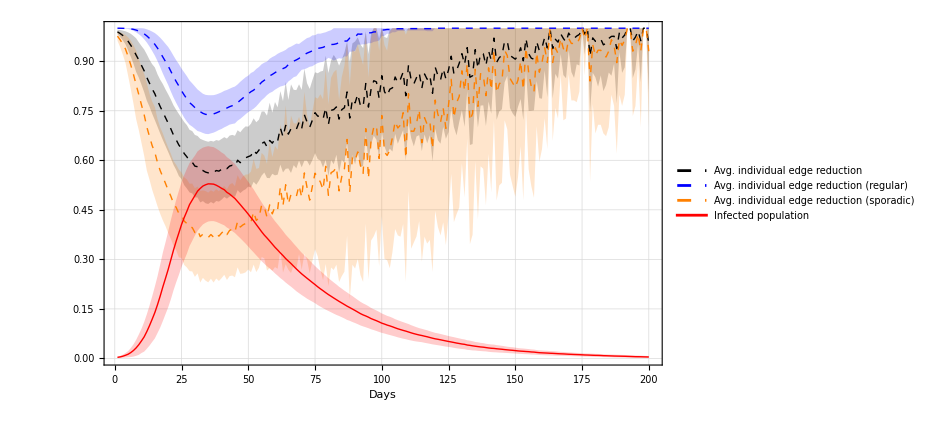

```mathematica
suscmean={0.989,0.984,0.978,0.971,0.9602,0.9481,0.9345,0.9185,0.9037,0.8874,0.871,0.8507,0.8334,0.8161,0.8014,0.7811,0.7627,0.7461,0.729,0.7124,0.695,0.6761,0.6619,0.6462,0.6356,0.6204,0.6105,0.5975,0.5941,0.5823,0.5806,0.5688,0.569,0.5642,0.562,0.5662,0.563,0.569,0.5672,0.5727,0.5796,0.5748,0.5825,0.5849,0.5816,0.6003,0.5928,0.6015,0.6075,0.6111,0.6143,0.6309,0.6207,0.6308,0.6506,0.6554,0.641,0.6601,0.6519,0.6655,0.6584,0.6982,0.6712,0.7057,0.6792,0.6958,0.6994,0.6941,0.7147,0.6962,0.7379,0.716,0.7,0.7216,0.7442,0.7337,0.7339,0.7248,0.759,0.7083,0.7513,0.7536,0.7617,0.7246,0.7534,0.7592,0.8071,0.7278,0.7849,0.7739,0.8003,0.7654,0.7616,0.8325,0.761,0.8162,0.841,0.8374,0.7874,0.8561,0.8078,0.7953,0.8152,0.8195,0.8523,0.8347,0.8458,0.8672,0.7953,0.8886,0.8434,0.8312,0.8505,0.8654,0.8185,0.8614,0.8453,0.8567,0.8029,0.882,0.8571,0.8436,0.8773,0.8464,0.8737,0.9152,0.8623,0.8723,0.8938,0.9229,0.8905,0.9412,0.8514,0.8561,0.9351,0.8783,0.9237,0.9229,0.8875,0.9311,0.9031,0.9701,0.8966,0.911,0.9175,0.9608,0.9604,0.9176,0.9119,0.9062,0.917,0.9408,0.9013,0.9687,0.9227,0.9091,0.9061,0.9602,0.9317,0.9407,0.9723,0.9402,1.0,0.9381,0.9665,0.9578,0.9831,0.9691,0.9579,0.9852,0.9716,0.969,0.9763,0.9812,1.0,0.9824,1.0,0.9153,0.9706,0.9604,0.9603,0.9675,0.9497,0.9546,0.9689,0.9752,0.9757,0.9381,0.9876,0.9704,0.9795,1.0,1.0,0.9614,0.9731,0.9917,0.9621,1.0,1.0,0.9547};
susclower={0.9825,0.9735,0.9634,0.9514,0.9331,0.9132,0.8923,0.8675,0.8502,0.8287,0.8064,0.7807,0.7623,0.741,0.7217,0.7017,0.6812,0.6615,0.6434,0.6252,0.606,0.586,0.5709,0.5522,0.5432,0.5247,0.5145,0.5028,0.4997,0.4878,0.4874,0.4725,0.4765,0.4699,0.4678,0.4737,0.4692,0.4768,0.4749,0.4807,0.4891,0.4839,0.4903,0.4929,0.489,0.5096,0.5007,0.5078,0.5124,0.5205,0.5176,0.5348,0.5261,0.5384,0.5537,0.563,0.5466,0.5459,0.5592,0.5544,0.5565,0.5869,0.5633,0.5742,0.5755,0.5617,0.5853,0.5756,0.5992,0.5789,0.5987,0.5987,0.5839,0.6003,0.6219,0.6037,0.5992,0.5786,0.6015,0.5523,0.6004,0.5881,0.6167,0.5625,0.6021,0.592,0.6546,0.5573,0.6159,0.5878,0.6282,0.5802,0.5833,0.6747,0.6001,0.6483,0.6746,0.6623,0.6064,0.6899,0.6424,0.6202,0.6352,0.6265,0.68,0.6502,0.6712,0.6914,0.5987,0.7151,0.6673,0.6422,0.6721,0.6763,0.6275,0.6785,0.6515,0.676,0.597,0.6958,0.6609,0.6503,0.7012,0.665,0.6854,0.7564,0.7011,0.6755,0.7157,0.7521,0.7012,0.8106,0.6464,0.6492,0.7868,0.6992,0.7657,0.7665,0.7039,0.778,0.7409,0.8756,0.7225,0.7481,0.7546,0.8359,0.8558,0.7586,0.7422,0.7312,0.7615,0.7856,0.722,0.8742,0.7494,0.7501,0.7513,0.8404,0.7881,0.7865,0.8723,0.7909,1.0,0.7868,0.8619,0.847,0.9218,0.8581,0.8485,0.9327,0.8674,0.8495,0.8908,0.8871,1.0,0.9199,1.0,0.7463,0.8651,0.8513,0.823,0.8572,0.8093,0.8283,0.8658,0.856,0.8927,0.7723,0.928,0.8647,0.8814,1.0,1.0,0.849,0.8751,0.952,0.8363,1.0,1.0,0.8038};
suscupper={0.9955,0.9945,0.9927,0.9906,0.9873,0.983,0.9767,0.9694,0.9573,0.9461,0.9357,0.9208,0.9045,0.8911,0.8812,0.8604,0.8441,0.8308,0.8146,0.7997,0.784,0.7663,0.7528,0.7403,0.7281,0.716,0.7065,0.6922,0.6885,0.6768,0.6737,0.6651,0.6615,0.6584,0.6562,0.6588,0.6568,0.6612,0.6594,0.6647,0.6701,0.6658,0.6748,0.6769,0.6743,0.691,0.6849,0.6951,0.7027,0.7018,0.7109,0.7271,0.7153,0.7231,0.7475,0.7478,0.7354,0.7744,0.7446,0.7765,0.7604,0.8094,0.7792,0.8373,0.7829,0.83,0.8134,0.8126,0.8301,0.8135,0.8771,0.8334,0.8162,0.8428,0.8665,0.8636,0.8687,0.8709,0.9164,0.8642,0.9022,0.9191,0.9067,0.8867,0.9047,0.9264,0.9596,0.8983,0.9539,0.96,0.9723,0.9506,0.9398,0.9903,0.9218,0.9842,1.0,1.0,0.9684,1.0,0.9732,0.9703,0.9951,1.0,1.0,1.0,1.0,1.0,0.9918,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0};

suscmean1={1.0,0.9999,0.9997,0.9994,0.9989,0.998,0.9965,0.9943,0.9914,0.9876,0.9829,0.9767,0.9691,0.9605,0.9511,0.9397,0.9268,0.9126,0.899,0.8855,0.8694,0.8532,0.8384,0.825,0.8105,0.7976,0.786,0.7747,0.7676,0.7596,0.7516,0.7471,0.7422,0.7391,0.7382,0.7392,0.7405,0.7434,0.747,0.7504,0.755,0.7583,0.7624,0.7653,0.7676,0.7748,0.7817,0.7885,0.7955,0.8013,0.8078,0.8124,0.82,0.8276,0.8365,0.8424,0.8482,0.8556,0.8601,0.8653,0.8706,0.8751,0.8778,0.8813,0.8897,0.8945,0.9003,0.904,0.9085,0.9164,0.92,0.9245,0.9279,0.9316,0.9345,0.9389,0.9402,0.942,0.9458,0.9507,0.9506,0.951,0.9529,0.9566,0.9563,0.9609,0.9613,0.9702,0.9707,0.9726,0.9824,0.9818,0.983,0.983,0.9859,0.9862,0.9887,0.9891,0.9907,0.9943,0.9949,0.9961,0.996,0.9974,0.9973,0.9984,0.9984,0.9984,0.9988,0.9988,0.9988,0.9988,0.9988,0.9988,0.9988,0.9987,0.9987,0.9987,0.9987,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0};
susclower1={0.9999,0.9998,0.9993,0.9987,0.9976,0.9953,0.9921,0.9876,0.9817,0.9753,0.9666,0.9567,0.9445,0.9312,0.917,0.9005,0.8822,0.8628,0.8453,0.8279,0.8083,0.7899,0.7737,0.7586,0.7433,0.729,0.7172,0.7076,0.7021,0.6955,0.6886,0.6863,0.6827,0.68,0.6792,0.6815,0.6838,0.6874,0.6917,0.695,0.6997,0.7036,0.708,0.71,0.7117,0.7199,0.7255,0.7323,0.7394,0.7461,0.7511,0.7562,0.7634,0.7726,0.782,0.789,0.7975,0.8037,0.8075,0.8138,0.8187,0.8233,0.8255,0.8283,0.8386,0.8447,0.8517,0.8545,0.8648,0.8741,0.8758,0.879,0.8833,0.8849,0.8901,0.8944,0.8969,0.8983,0.9037,0.9101,0.9072,0.902,0.9057,0.9091,0.9076,0.9146,0.9142,0.9287,0.9291,0.9318,0.9508,0.9499,0.9513,0.9514,0.9546,0.9546,0.9588,0.9601,0.9628,0.9761,0.9769,0.9834,0.9832,0.9878,0.9876,0.9915,0.9915,0.9915,0.9932,0.9932,0.9932,0.9932,0.9932,0.9932,0.9932,0.9931,0.991,0.9909,0.9909,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0};
suscupper1={1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,0.9992,0.9967,0.9937,0.9898,0.9853,0.9789,0.9713,0.9624,0.9527,0.9431,0.9306,0.9165,0.903,0.8913,0.8777,0.8662,0.8548,0.8417,0.833,0.8238,0.8145,0.8079,0.8016,0.7982,0.7971,0.797,0.7973,0.7993,0.8024,0.8058,0.8103,0.813,0.8167,0.8205,0.8234,0.8297,0.8378,0.8448,0.8515,0.8564,0.8644,0.8686,0.8767,0.8826,0.8909,0.8957,0.8989,0.9075,0.9127,0.9167,0.9226,0.9268,0.9301,0.9343,0.9408,0.9443,0.9488,0.9535,0.9523,0.9586,0.9643,0.9701,0.9726,0.9783,0.9788,0.9834,0.9835,0.9857,0.9878,0.9912,0.994,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0};

suscmean2={0.9759,0.965,0.9518,0.937,0.914,0.8884,0.8599,0.8285,0.7986,0.7675,0.7378,0.7008,0.6717,0.6444,0.624,0.5929,0.5688,0.5496,0.5298,0.5091,0.4911,0.4693,0.457,0.4388,0.4336,0.4157,0.4086,0.3966,0.3964,0.3812,0.3889,0.3687,0.3763,0.3711,0.3663,0.3752,0.3672,0.3772,0.3704,0.3798,0.3876,0.375,0.3878,0.3911,0.3837,0.4153,0.3979,0.4045,0.4088,0.4133,0.4134,0.4439,0.4178,0.4258,0.4648,0.4586,0.4277,0.465,0.4378,0.46,0.4517,0.5185,0.4628,0.5259,0.4679,0.4967,0.4975,0.4909,0.5236,0.4882,0.5618,0.5177,0.4794,0.5211,0.5609,0.5481,0.5341,0.511,0.5817,0.4942,0.5624,0.5674,0.5791,0.5074,0.5502,0.5746,0.6632,0.503,0.6089,0.6002,0.6255,0.5843,0.5604,0.6959,0.5449,0.6635,0.7002,0.7054,0.6055,0.7356,0.6253,0.6147,0.6308,0.6697,0.7175,0.6978,0.707,0.7441,0.6067,0.8015,0.6881,0.6881,0.7115,0.7533,0.6533,0.7291,0.7086,0.7176,0.6353,0.7824,0.7394,0.7152,0.7576,0.6968,0.7677,0.8452,0.729,0.7742,0.7935,0.871,0.8108,0.8925,0.7204,0.7419,0.8753,0.7634,0.8624,0.8581,0.7956,0.88,0.8133,0.9333,0.8044,0.8311,0.84,0.9333,0.9172,0.8483,0.8345,0.8207,0.8429,0.9,0.8143,0.9407,0.8667,0.8222,0.8074,0.9259,0.8667,0.8963,0.9407,0.8963,1.0,0.8963,0.9407,0.9231,0.9692,0.9385,0.9231,0.9692,0.9538,0.9538,0.952,0.968,1.0,0.968,1.0,0.84,0.95,0.9167,0.9333,0.9333,0.9167,0.913,0.9304,0.9652,0.9478,0.8957,0.9652,0.9478,0.9652,1.0,1.0,0.9304,0.9478,0.9826,0.9304,1.0,1.0,0.9304};
susclower2={0.9619,0.9427,0.9201,0.8949,0.8556,0.8146,0.7716,0.7244,0.6911,0.6526,0.6138,0.5687,0.5414,0.5108,0.4862,0.4608,0.4381,0.4179,0.4006,0.3798,0.3622,0.3406,0.3275,0.3058,0.3043,0.2831,0.2754,0.2643,0.2635,0.2471,0.2575,0.2299,0.2439,0.2355,0.2305,0.2413,0.2299,0.242,0.2346,0.2431,0.2533,0.2375,0.2493,0.251,0.2458,0.2757,0.2562,0.2574,0.2607,0.2695,0.2609,0.2839,0.2615,0.2749,0.3071,0.3032,0.266,0.2738,0.2655,0.2767,0.2717,0.3287,0.2601,0.2854,0.2687,0.2585,0.2828,0.2704,0.3158,0.2685,0.3164,0.298,0.258,0.2951,0.3308,0.3095,0.2682,0.2374,0.2859,0.2192,0.2753,0.2679,0.2839,0.2315,0.2489,0.2626,0.3713,0.1785,0.2836,0.2722,0.3016,0.2526,0.2317,0.4085,0.2393,0.3571,0.3701,0.39,0.2793,0.4313,0.3016,0.2974,0.2734,0.3227,0.3919,0.3727,0.3687,0.4071,0.2328,0.5066,0.3322,0.3512,0.3694,0.4155,0.293,0.3685,0.3477,0.3588,0.262,0.4471,0.3985,0.3723,0.412,0.3432,0.4327,0.559,0.4126,0.4366,0.457,0.5903,0.4882,0.6656,0.3459,0.3745,0.5979,0.4214,0.5817,0.5743,0.4639,0.6195,0.5029,0.7211,0.4783,0.524,0.5319,0.7211,0.6935,0.5572,0.5225,0.4897,0.5479,0.6418,0.4791,0.7583,0.5731,0.5218,0.4864,0.703,0.5949,0.6339,0.7272,0.6339,1.0,0.6585,0.7583,0.7265,0.8605,0.7211,0.7265,0.8605,0.7813,0.7813,0.7761,0.808,1.0,0.8572,1.0,0.5345,0.7706,0.6814,0.7075,0.7075,0.6814,0.6731,0.7,0.7984,0.7647,0.6202,0.7984,0.7647,0.7984,1.0,1.0,0.734,0.7647,0.8992,0.7,1.0,1.0,0.7};
suscupper2={0.9899,0.9873,0.9836,0.9792,0.9724,0.9621,0.9483,0.9325,0.9062,0.8824,0.8618,0.833,0.802,0.7779,0.7617,0.725,0.6996,0.6814,0.659,0.6383,0.6199,0.5979,0.5865,0.5718,0.5629,0.5483,0.5418,0.529,0.5294,0.5153,0.5203,0.5074,0.5088,0.5067,0.5021,0.5092,0.5046,0.5123,0.5063,0.5165,0.5219,0.5124,0.5263,0.5312,0.5216,0.5549,0.5396,0.5515,0.5569,0.5572,0.5659,0.604,0.574,0.5767,0.6224,0.614,0.5894,0.6563,0.6102,0.6434,0.6317,0.7083,0.6654,0.7663,0.6671,0.7349,0.7122,0.7113,0.7314,0.708,0.8071,0.7374,0.7009,0.747,0.791,0.7867,0.8,0.7845,0.8775,0.7692,0.8496,0.8669,0.8744,0.7833,0.8515,0.8866,0.9551,0.8276,0.9341,0.9281,0.9494,0.9159,0.8892,0.9833,0.8504,0.9699,1.0,1.0,0.9317,1.0,0.9491,0.932,0.9881,1.0,1.0,1.0,1.0,1.0,0.9805,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0};

imean={0.0033,0.0046,0.0067,0.0095,0.0128,0.0178,0.0241,0.032,0.0417,0.0532,0.0654,0.0814,0.0994,0.1188,0.139,0.1628,0.1888,0.2168,0.2429,0.2696,0.299,0.3285,0.3553,0.3802,0.4056,0.4267,0.4457,0.466,0.4796,0.4931,0.5066,0.5149,0.522,0.5259,0.5287,0.5284,0.5278,0.5245,0.5201,0.5151,0.5109,0.5029,0.4978,0.491,0.4843,0.475,0.4658,0.4561,0.4468,0.4368,0.4264,0.4166,0.4054,0.3946,0.3836,0.3735,0.3648,0.3556,0.3461,0.3366,0.3283,0.3196,0.3114,0.3024,0.2948,0.2873,0.2791,0.271,0.2634,0.256,0.2494,0.2428,0.2364,0.2299,0.2236,0.2169,0.2108,0.2051,0.1991,0.1934,0.1883,0.183,0.1779,0.1728,0.168,0.1632,0.1583,0.154,0.1496,0.1451,0.1404,0.1357,0.1318,0.1286,0.1249,0.1206,0.1174,0.1142,0.1106,0.1068,0.1041,0.101,0.0986,0.0958,0.0927,0.0898,0.0873,0.0849,0.0827,0.0801,0.0775,0.0751,0.073,0.071,0.0694,0.0674,0.0656,0.0634,0.0613,0.0594,0.058,0.0564,0.0547,0.053,0.0514,0.0499,0.0483,0.0466,0.0452,0.0437,0.0427,0.0406,0.0396,0.0382,0.037,0.0359,0.0348,0.0341,0.0329,0.0317,0.0308,0.0303,0.0293,0.0285,0.0278,0.0268,0.026,0.0252,0.0246,0.0237,0.0228,0.0221,0.0216,0.021,0.0205,0.0196,0.0192,0.0182,0.0174,0.017,0.0166,0.0162,0.0157,0.0154,0.0149,0.0144,0.014,0.0137,0.0132,0.0127,0.0124,0.012,0.0117,0.0114,0.011,0.0105,0.0103,0.01,0.0096,0.0093,0.0092,0.0089,0.0084,0.0082,0.0079,0.0076,0.0073,0.0071,0.0069,0.0067,0.0065,0.0062,0.0059,0.0056,0.0053,0.0052,0.0051,0.0048,0.0046,0.0044};
ilower={0.0017,0.0017,0.002,0.0028,0.0034,0.0041,0.0056,0.0079,0.0108,0.0164,0.0206,0.0292,0.0388,0.0498,0.0606,0.0768,0.0934,0.1132,0.1341,0.1548,0.179,0.2063,0.2306,0.2529,0.2772,0.2978,0.3171,0.3403,0.356,0.3722,0.3862,0.3966,0.4057,0.4108,0.4147,0.4158,0.4158,0.4137,0.4103,0.4066,0.4031,0.3963,0.3917,0.3855,0.3798,0.3718,0.364,0.3559,0.3477,0.3387,0.3296,0.3211,0.3121,0.3035,0.2945,0.2867,0.2793,0.2723,0.2656,0.2576,0.2507,0.2433,0.2371,0.2298,0.2234,0.2172,0.2105,0.2035,0.1977,0.1919,0.1866,0.181,0.1763,0.1719,0.1672,0.1617,0.1569,0.1523,0.1478,0.1438,0.1398,0.1357,0.1318,0.1286,0.1248,0.121,0.1166,0.1139,0.1103,0.1072,0.1037,0.0999,0.097,0.0944,0.0915,0.0883,0.0858,0.0831,0.0802,0.0774,0.0755,0.073,0.0709,0.0687,0.0664,0.0639,0.0618,0.0598,0.0582,0.056,0.0543,0.0526,0.0513,0.0502,0.0492,0.0474,0.0459,0.0443,0.0426,0.0414,0.04,0.0388,0.0373,0.0358,0.0349,0.0337,0.0321,0.0307,0.0296,0.0286,0.0279,0.0261,0.0253,0.0243,0.024,0.023,0.0224,0.0217,0.0213,0.0201,0.0192,0.0187,0.0183,0.0176,0.0174,0.0168,0.0164,0.0158,0.0154,0.0149,0.0141,0.0137,0.0132,0.0128,0.0125,0.0118,0.0116,0.011,0.0104,0.0101,0.0097,0.0093,0.009,0.0088,0.0083,0.0082,0.008,0.0078,0.0076,0.0073,0.0068,0.0067,0.0065,0.0063,0.0061,0.0057,0.0056,0.0053,0.0048,0.0048,0.0047,0.0045,0.0041,0.004,0.0038,0.0035,0.0031,0.003,0.0028,0.0026,0.0025,0.0022,0.0021,0.0019,0.0017,0.0016,0.0017,0.0017,0.0017,0.0014};
iupper={0.0049,0.0075,0.0113,0.0162,0.0223,0.0315,0.0426,0.0562,0.0726,0.0899,0.1102,0.1336,0.1599,0.1879,0.2175,0.2487,0.2841,0.3205,0.3517,0.3845,0.4191,0.4506,0.48,0.5074,0.534,0.5556,0.5743,0.5917,0.6031,0.614,0.627,0.6333,0.6383,0.641,0.6427,0.641,0.6398,0.6353,0.6299,0.6237,0.6186,0.6095,0.6038,0.5964,0.5888,0.5782,0.5676,0.5562,0.546,0.5349,0.5232,0.5121,0.4986,0.4858,0.4726,0.4603,0.4503,0.4389,0.4266,0.4156,0.4059,0.3958,0.3857,0.375,0.3661,0.3574,0.3476,0.3386,0.3292,0.3202,0.3123,0.3045,0.2965,0.2879,0.2799,0.2721,0.2648,0.2579,0.2505,0.2431,0.2367,0.2302,0.224,0.2171,0.2113,0.2053,0.1999,0.1941,0.189,0.183,0.1771,0.1715,0.1667,0.1628,0.1582,0.1529,0.1489,0.1452,0.141,0.1363,0.1327,0.129,0.1264,0.123,0.119,0.1158,0.1128,0.1099,0.1071,0.1042,0.1007,0.0976,0.0946,0.0918,0.0897,0.0874,0.0853,0.0825,0.08,0.0775,0.076,0.0741,0.072,0.0701,0.0678,0.0661,0.0644,0.0625,0.0607,0.0588,0.0575,0.055,0.0538,0.0522,0.05,0.0489,0.0472,0.0464,0.0445,0.0433,0.0424,0.0419,0.0403,0.0393,0.0382,0.0369,0.0355,0.0345,0.0339,0.0326,0.0315,0.0305,0.03,0.0292,0.0284,0.0274,0.0268,0.0254,0.0245,0.024,0.0235,0.0231,0.0223,0.022,0.0215,0.0207,0.0199,0.0196,0.0188,0.0181,0.0179,0.0173,0.0168,0.0166,0.0158,0.0152,0.015,0.0147,0.0145,0.0139,0.0137,0.0133,0.0126,0.0123,0.012,0.0118,0.0115,0.0112,0.011,0.0107,0.0105,0.0102,0.0097,0.0094,0.0089,0.0088,0.0085,0.008,0.0076,0.0074};

SporadicPlot1= ListLinePlot[ {
suscmean,susclower,suscupper,
suscmean1,susclower1,suscupper1,
suscmean2,susclower2,suscupper2,
imean,ilower,iupper
}, Filling->{
{1->{2}},{1->{3}}, 
{4->{5}},{4->{6}},
{7->{8}},{7->{9}}, 
{10->{11}},{10->{12}}
},
PlotStyle->{ 
Directive[Thick,Dashed,Black],None,None,
Directive[Thick,Dashed,Blue],None,None,
Directive[Thick,Dashed,Orange],None,None,
Directive[Thick,Red],None,None
},
Frame->{True,True,False,False},
Axes->False,
FrameLabel->{Style["Days", Black, 14 ]},
LabelStyle->Directive[Bold, Medium, Black],
PlotRange->{{0,201}, {0,1}},
TicksStyle->Directive[Bold, 12],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],
PlotLegends->Placed[{
Style["Avg. individual edge reduction",FontFamily->"Century",18],None, None, 
Style["Avg. individual edge reduction (regular)",FontFamily->"Century",18], None, None,
Style["Avg. individual edge reduction (sporadic)",FontFamily->"Century",18],None, None, 
Style["Infected population",FontFamily->"Century",18],None, None
}, Below],
ImageSize->700
];
Export["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/adaptive_networks/Figures/article_figures/SporadicPlot1.pdf",SporadicPlot1,"PDF","AllowRasterization"->False];
SporadicPlot1
```

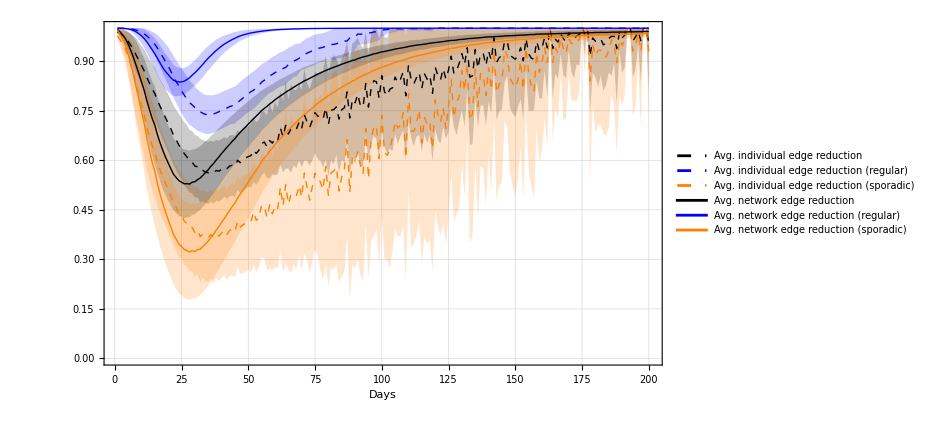

```mathematica
mean={0.9962,0.9886,0.9791,0.9681,0.9517,0.9327,0.9112,0.887,0.8627,0.8369,0.8118,0.7806,0.7532,0.7272,0.7059,0.6767,0.6521,0.6301,0.6099,0.5918,0.5744,0.5575,0.5477,0.5384,0.5335,0.529,0.5291,0.5282,0.5338,0.535,0.5415,0.5463,0.5545,0.5633,0.5715,0.582,0.5903,0.601,0.6102,0.6206,0.6298,0.6396,0.6482,0.6578,0.6655,0.676,0.6848,0.6934,0.7011,0.7097,0.7181,0.7262,0.7339,0.7419,0.7505,0.7572,0.7633,0.7707,0.7763,0.7833,0.7892,0.7949,0.8001,0.8059,0.8111,0.8158,0.821,0.8261,0.8311,0.8356,0.8407,0.844,0.8482,0.8524,0.8567,0.8608,0.8644,0.8684,0.8717,0.8753,0.8784,0.8817,0.8846,0.8877,0.8909,0.8938,0.8966,0.8992,0.9023,0.9042,0.9077,0.9103,0.913,0.9148,0.917,0.9195,0.9222,0.9237,0.9261,0.9282,0.9295,0.9314,0.9331,0.9349,0.9369,0.9383,0.9397,0.941,0.9425,0.9445,0.9459,0.9474,0.9486,0.9498,0.9506,0.9518,0.9529,0.9547,0.9553,0.9566,0.9573,0.9586,0.9595,0.9608,0.962,0.963,0.9632,0.9641,0.9656,0.9662,0.9669,0.9681,0.9688,0.9693,0.97,0.9705,0.9714,0.9722,0.9729,0.9737,0.9736,0.9743,0.9748,0.9753,0.9756,0.9766,0.9771,0.9772,0.9776,0.978,0.9786,0.9792,0.9793,0.9796,0.9804,0.9808,0.9808,0.9819,0.9821,0.9824,0.9826,0.9826,0.983,0.9833,0.9834,0.9838,0.984,0.9842,0.9845,0.985,0.9851,0.9852,0.9855,0.9853,0.986,0.9858,0.9865,0.9865,0.9865,0.9872,0.9869,0.9873,0.9873,0.9872,0.9874,0.988,0.9881,0.988,0.9884,0.9883,0.9885,0.9887,0.9892,0.989,0.9891,0.9894,0.9895,0.9901,0.9901,0.99};
lower={0.99,0.9762,0.9598,0.9415,0.9136,0.8824,0.849,0.812,0.7816,0.7486,0.7143,0.6756,0.6456,0.6147,0.5884,0.5616,0.5363,0.5125,0.4946,0.4779,0.4622,0.4483,0.4398,0.431,0.4293,0.4251,0.4268,0.4277,0.4347,0.4366,0.4445,0.4498,0.4589,0.4691,0.4782,0.4906,0.4998,0.5125,0.5228,0.5357,0.5463,0.5581,0.5678,0.579,0.5879,0.6005,0.6114,0.6212,0.6302,0.6405,0.6503,0.6602,0.6692,0.6792,0.6897,0.6986,0.7052,0.7149,0.7223,0.7306,0.7376,0.7442,0.7507,0.7576,0.7638,0.7692,0.7757,0.781,0.7877,0.7929,0.7989,0.803,0.8083,0.8136,0.8191,0.824,0.8285,0.8333,0.8376,0.8421,0.8461,0.8499,0.8536,0.8578,0.8616,0.8654,0.8683,0.8717,0.8756,0.8781,0.8823,0.8855,0.8886,0.891,0.8937,0.8969,0.9002,0.9015,0.9045,0.9075,0.9093,0.9112,0.9132,0.9153,0.9179,0.9191,0.9212,0.9225,0.9246,0.927,0.9288,0.9307,0.9321,0.9345,0.935,0.9366,0.9374,0.9398,0.9408,0.9424,0.9432,0.9446,0.9456,0.947,0.9489,0.9501,0.9503,0.9514,0.9531,0.9535,0.9546,0.9561,0.957,0.9576,0.9587,0.9589,0.9606,0.9612,0.9623,0.9632,0.9631,0.9639,0.9642,0.9652,0.9653,0.967,0.9676,0.9676,0.9682,0.9685,0.9696,0.9704,0.9701,0.9706,0.9713,0.972,0.9719,0.9732,0.9736,0.9738,0.9743,0.9743,0.975,0.975,0.9756,0.9758,0.9763,0.9762,0.9766,0.9773,0.977,0.9772,0.9773,0.9777,0.9778,0.9784,0.979,0.9787,0.979,0.9797,0.9789,0.9801,0.9797,0.9794,0.98,0.9807,0.9804,0.9805,0.9808,0.981,0.9813,0.981,0.9821,0.9815,0.9818,0.9818,0.9824,0.9831,0.9834,0.983};
upper={1.0,1.0,0.9983,0.9947,0.9899,0.9831,0.9735,0.9621,0.9439,0.9251,0.9094,0.8857,0.8609,0.8396,0.8233,0.7917,0.7679,0.7476,0.7251,0.7058,0.6865,0.6666,0.6555,0.6457,0.6377,0.6329,0.6313,0.6287,0.6328,0.6334,0.6385,0.6427,0.65,0.6576,0.6649,0.6733,0.6808,0.6895,0.6977,0.7056,0.7133,0.7211,0.7286,0.7366,0.743,0.7514,0.7583,0.7655,0.7721,0.7789,0.786,0.7923,0.7986,0.8046,0.8114,0.8159,0.8213,0.8266,0.8303,0.8361,0.8408,0.8455,0.8495,0.8542,0.8584,0.8624,0.8664,0.8712,0.8746,0.8783,0.8826,0.8849,0.8882,0.8911,0.8942,0.8977,0.9004,0.9034,0.9058,0.9084,0.9108,0.9134,0.9157,0.9176,0.9203,0.9222,0.9249,0.9267,0.9291,0.9304,0.9331,0.9351,0.9374,0.9385,0.9403,0.942,0.9443,0.9458,0.9477,0.949,0.9498,0.9515,0.953,0.9546,0.9558,0.9576,0.9583,0.9594,0.9604,0.9621,0.9629,0.9642,0.9652,0.965,0.9663,0.9671,0.9683,0.9695,0.9697,0.9708,0.9713,0.9726,0.9734,0.9747,0.975,0.976,0.976,0.9768,0.9781,0.9788,0.9792,0.9801,0.9806,0.981,0.9812,0.982,0.9822,0.9833,0.9834,0.9843,0.9841,0.9847,0.9854,0.9854,0.9858,0.9863,0.9865,0.9867,0.9871,0.9876,0.9875,0.988,0.9885,0.9887,0.9894,0.9896,0.9897,0.9906,0.9906,0.991,0.9909,0.991,0.9909,0.9915,0.9912,0.9918,0.9917,0.9923,0.9924,0.9928,0.9932,0.9933,0.9937,0.993,0.9942,0.9932,0.9939,0.9942,0.994,0.9948,0.9949,0.9946,0.9949,0.995,0.9947,0.9953,0.9958,0.9955,0.9959,0.9956,0.9956,0.9964,0.9964,0.9965,0.9965,0.9971,0.9965,0.9971,0.9968,0.997};

mean1={1.0,0.9998,0.9994,0.9989,0.9978,0.9959,0.9929,0.9888,0.9833,0.9766,0.9686,0.9584,0.9467,0.9345,0.9224,0.9084,0.8942,0.8805,0.8687,0.8596,0.85,0.8424,0.8386,0.8375,0.8373,0.8397,0.8444,0.85,0.8579,0.865,0.8731,0.882,0.891,0.9005,0.9094,0.9172,0.9251,0.9327,0.9393,0.9459,0.9519,0.9566,0.9612,0.9657,0.9696,0.9735,0.9769,0.9794,0.9817,0.9837,0.9857,0.9871,0.9885,0.9898,0.9909,0.992,0.9929,0.9938,0.9944,0.9952,0.9957,0.9961,0.9965,0.9967,0.9972,0.9975,0.9977,0.9979,0.9981,0.9984,0.9985,0.9987,0.9989,0.999,0.9991,0.9992,0.9993,0.9993,0.9994,0.9995,0.9995,0.9995,0.9996,0.9996,0.9996,0.9997,0.9997,0.9998,0.9998,0.9998,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0};
lower1={0.9998,0.9994,0.9986,0.9974,0.9951,0.9906,0.9844,0.976,0.9654,0.9544,0.9408,0.9258,0.9086,0.8915,0.875,0.8579,0.8411,0.8261,0.8146,0.8071,0.7994,0.7951,0.7941,0.7948,0.7962,0.7999,0.8058,0.8118,0.82,0.8267,0.8341,0.8428,0.8514,0.8621,0.8726,0.8812,0.8905,0.9,0.9087,0.9178,0.9258,0.9325,0.9387,0.945,0.9504,0.9566,0.9615,0.9653,0.9689,0.9726,0.9755,0.9782,0.9802,0.9825,0.9843,0.9861,0.9878,0.9892,0.9902,0.9917,0.9926,0.9932,0.9938,0.9941,0.9949,0.9954,0.9959,0.9961,0.9965,0.9969,0.9971,0.9975,0.998,0.9981,0.9982,0.9984,0.9985,0.9987,0.9987,0.9989,0.9989,0.999,0.999,0.9991,0.9991,0.9993,0.9993,0.9994,0.9994,0.9995,0.9996,0.9996,0.9996,0.9996,0.9997,0.9997,0.9998,0.9998,0.9998,0.9998,0.9998,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,0.9999,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0};
upper1={1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,0.9987,0.9964,0.991,0.9848,0.9776,0.9698,0.9589,0.9473,0.935,0.9229,0.9122,0.9007,0.8898,0.883,0.8803,0.8785,0.8795,0.8831,0.8882,0.8959,0.9032,0.9122,0.9213,0.9305,0.9389,0.9463,0.9531,0.9598,0.9653,0.9699,0.9741,0.978,0.9806,0.9837,0.9864,0.9887,0.9903,0.9923,0.9936,0.9946,0.9948,0.9959,0.996,0.9968,0.997,0.9976,0.9979,0.998,0.9984,0.9985,0.9988,0.9989,0.9991,0.9991,0.9994,0.9994,0.9995,0.9995,0.9997,0.9997,0.9998,0.9999,0.9999,0.9998,0.9999,0.9999,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0};

mean2={0.9938,0.9814,0.966,0.9483,0.9221,0.8921,0.8588,0.8216,0.7853,0.7472,0.7112,0.6666,0.6291,0.5941,0.567,0.5281,0.4969,0.4695,0.4439,0.4202,0.3977,0.3749,0.3612,0.3466,0.3389,0.33,0.327,0.322,0.326,0.3235,0.329,0.3311,0.3389,0.3473,0.3551,0.3672,0.3758,0.3885,0.3994,0.4123,0.4235,0.4366,0.4477,0.4606,0.4707,0.4855,0.4978,0.5102,0.5214,0.5343,0.5468,0.5592,0.5709,0.5832,0.5966,0.6069,0.6163,0.628,0.6367,0.6476,0.657,0.6661,0.6744,0.6837,0.692,0.6995,0.7079,0.7161,0.7242,0.7314,0.7398,0.7449,0.7518,0.7585,0.7655,0.7723,0.7782,0.7845,0.79,0.7958,0.801,0.8062,0.8111,0.8161,0.8214,0.826,0.8306,0.8348,0.84,0.8431,0.8487,0.853,0.8574,0.8603,0.8639,0.868,0.8725,0.8749,0.8789,0.8823,0.8845,0.8874,0.8903,0.8933,0.8965,0.8989,0.9012,0.9032,0.9057,0.909,0.9112,0.9138,0.9158,0.9176,0.9191,0.921,0.9228,0.9257,0.9267,0.9288,0.9299,0.9321,0.9336,0.9358,0.9376,0.9394,0.9396,0.9411,0.9436,0.9445,0.9457,0.9477,0.9488,0.9497,0.9507,0.9516,0.9531,0.9545,0.9555,0.957,0.9567,0.9579,0.9587,0.9595,0.96,0.9617,0.9624,0.9626,0.9633,0.964,0.9649,0.9659,0.9661,0.9666,0.9679,0.9685,0.9685,0.9703,0.9707,0.9711,0.9715,0.9715,0.9721,0.9726,0.9728,0.9735,0.9738,0.9742,0.9746,0.9755,0.9756,0.9758,0.9763,0.976,0.9771,0.9767,0.9778,0.9778,0.9779,0.9791,0.9785,0.9792,0.9792,0.9791,0.9793,0.9803,0.9805,0.9804,0.9809,0.9809,0.9811,0.9816,0.9824,0.982,0.9822,0.9827,0.9828,0.9838,0.9838,0.9836};
lower2={0.9836,0.9611,0.9348,0.9054,0.8608,0.8123,0.7613,0.7058,0.6623,0.615,0.5671,0.5127,0.4746,0.4346,0.4024,0.369,0.3385,0.3092,0.2874,0.2649,0.2444,0.2244,0.2112,0.1963,0.192,0.1824,0.1807,0.1778,0.1831,0.1814,0.1885,0.1908,0.2002,0.2101,0.2185,0.2331,0.2424,0.2574,0.2695,0.285,0.2979,0.3133,0.3255,0.3403,0.3519,0.3691,0.3841,0.3981,0.4108,0.4258,0.4402,0.4551,0.4688,0.4839,0.5,0.5135,0.5236,0.5386,0.5502,0.5629,0.574,0.5845,0.5948,0.6059,0.6156,0.6242,0.6346,0.6432,0.6539,0.6624,0.6721,0.6786,0.687,0.6957,0.7046,0.7125,0.7198,0.7276,0.7346,0.742,0.7484,0.7546,0.7606,0.7674,0.7737,0.7798,0.7846,0.7901,0.7965,0.8005,0.8073,0.8127,0.8177,0.8216,0.826,0.8313,0.8366,0.8388,0.8437,0.8486,0.8514,0.8546,0.8579,0.8613,0.8656,0.8675,0.871,0.8731,0.8765,0.8804,0.8834,0.8865,0.8888,0.8928,0.8936,0.8962,0.8976,0.9014,0.9031,0.9057,0.907,0.9093,0.911,0.9133,0.9163,0.9183,0.9187,0.9204,0.9232,0.924,0.9256,0.9282,0.9297,0.9306,0.9324,0.9327,0.9355,0.9365,0.9383,0.9399,0.9396,0.9409,0.9415,0.943,0.9433,0.946,0.947,0.947,0.9479,0.9485,0.9503,0.9516,0.951,0.9519,0.9531,0.9541,0.9541,0.9561,0.9568,0.9571,0.958,0.958,0.9591,0.9591,0.9602,0.9604,0.9612,0.9611,0.9618,0.9629,0.9624,0.9627,0.9629,0.9636,0.9637,0.9646,0.9657,0.9652,0.9656,0.9668,0.9655,0.9674,0.9667,0.9664,0.9674,0.9684,0.9679,0.9682,0.9686,0.969,0.9694,0.969,0.9707,0.9698,0.9703,0.9703,0.9713,0.9724,0.9728,0.9722};
upper2={1.0,1.0,0.9972,0.9912,0.9833,0.9719,0.9562,0.9375,0.9083,0.8793,0.8553,0.8204,0.7837,0.7537,0.7315,0.6872,0.6552,0.6299,0.6005,0.5754,0.5511,0.5254,0.5113,0.4969,0.4857,0.4776,0.4732,0.4661,0.469,0.4656,0.4695,0.4715,0.4775,0.4846,0.4916,0.5014,0.5091,0.5197,0.5294,0.5395,0.5491,0.5599,0.57,0.581,0.5896,0.6019,0.6116,0.6223,0.632,0.6427,0.6533,0.6633,0.673,0.6825,0.6931,0.7003,0.7089,0.7173,0.7232,0.7323,0.74,0.7476,0.754,0.7616,0.7684,0.7747,0.7812,0.7889,0.7945,0.8005,0.8074,0.8112,0.8165,0.8214,0.8264,0.832,0.8365,0.8415,0.8454,0.8496,0.8536,0.8578,0.8616,0.8647,0.8691,0.8723,0.8766,0.8796,0.8835,0.8857,0.89,0.8933,0.8971,0.899,0.9019,0.9047,0.9084,0.911,0.9141,0.9161,0.9175,0.9203,0.9227,0.9253,0.9274,0.9303,0.9314,0.9333,0.9348,0.9376,0.9391,0.9411,0.9428,0.9425,0.9446,0.9459,0.9479,0.9499,0.9502,0.9519,0.9528,0.955,0.9562,0.9583,0.9589,0.9605,0.9606,0.9619,0.964,0.9651,0.9658,0.9673,0.968,0.9688,0.9691,0.9704,0.9707,0.9725,0.9727,0.9741,0.9738,0.9749,0.976,0.976,0.9766,0.9774,0.9778,0.9781,0.9788,0.9796,0.9794,0.9803,0.9811,0.9814,0.9826,0.9828,0.983,0.9846,0.9845,0.9851,0.985,0.9851,0.9851,0.986,0.9855,0.9865,0.9864,0.9872,0.9875,0.9881,0.9887,0.989,0.9896,0.9884,0.9904,0.9888,0.9899,0.9904,0.9902,0.9913,0.9916,0.991,0.9916,0.9918,0.9913,0.9922,0.9931,0.9925,0.9932,0.9928,0.9928,0.9941,0.994,0.9942,0.9942,0.9951,0.9942,0.9952,0.9948,0.9951};

SporadicPlot2= ListLinePlot[ {
suscmean,susclower,suscupper,
suscmean1,susclower1,suscupper1,
suscmean2,susclower2,suscupper2,
mean,lower,upper,
mean1,lower1,upper1,
mean2,lower2,upper2
}, Filling->{
{1->{2}},{1->{3}}, 
{4->{5}},{4->{6}},
{7->{8}},{7->{9}}, 
{10->{11}},{10->{12}}, 
{13->{14}},{13->{15}}, 
{16->{17}},{16->{18}}
},
PlotStyle->{ 
Directive[Thick,Dashed,Black],None,None,
Directive[Thick,Dashed,Blue],None,None,
Directive[Thick,Dashed,Orange],None,None,
Directive[Thick,Black],None,None,
Directive[Thick,Blue],None,None,
Directive[Thick,Orange],None,None
},
Frame->{True,True,False,False},
Axes->False,
FrameLabel->{Style["Days", Black, 14 ]},
LabelStyle->Directive[Bold, Medium, Black],
PlotRange->{{0,201}, {0,1}},
TicksStyle->Directive[Bold, 12],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],
PlotLegends->Placed[{
Style["Avg. individual edge reduction",FontFamily->"Century",18],None, None, 
Style["Avg. individual edge reduction (regular)",FontFamily->"Century",18], None, None,
Style["Avg. individual edge reduction (sporadic)",FontFamily->"Century",18],None, None,
Style["Avg. network edge reduction",FontFamily->"Century",18],None, None, 
Style["Avg. network edge reduction (regular)",FontFamily->"Century",18], None, None,
Style["Avg. network edge reduction (sporadic)",FontFamily->"Century",18],None, None
}, Below],
ImageSize->700
];
Export["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/adaptive_networks/Figures/article_figures/SporadicPlot2.pdf",SporadicPlot2,"PDF","AllowRasterization"->False];
SporadicPlot2
```

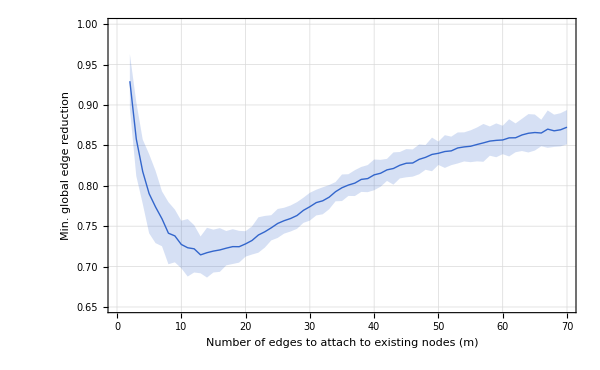

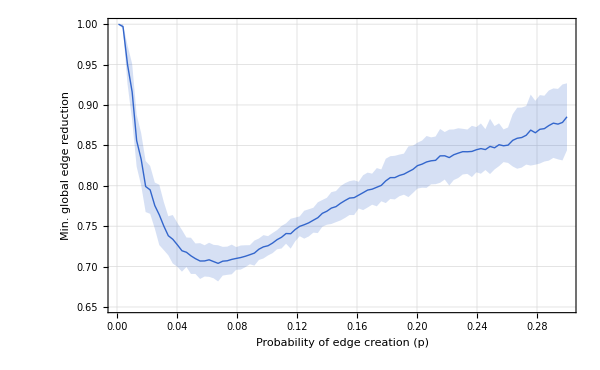

```mathematica
peds={0.001,0.004,0.007,0.0101,0.0131,0.0161,0.0191,0.0221,0.0252,0.0282,0.0312,0.0342,0.0372,0.0403,0.0433,0.0463,0.0493,0.0523,0.0554,0.0584,0.0614,0.0644,0.0674,0.0705,0.0735,0.0765,0.0795,0.0825,0.0856,0.0886,0.0916,0.0946,0.0976,0.1007,0.1037,0.1067,0.1097,0.1127,0.1158,0.1188,0.1218,0.1248,0.1278,0.1309,0.1339,0.1369,0.1399,0.1429,0.146,0.149,0.152,0.155,0.1581,0.1611,0.1641,0.1671,0.1701,0.1732,0.1762,0.1792,0.1822,0.1852,0.1883,0.1913,0.1943,0.1973,0.2003,0.2034,0.2064,0.2094,0.2124,0.2154,0.2185,0.2215,0.2245,0.2275,0.2305,0.2336,0.2366,0.2396,0.2426,0.2456,0.2487,0.2517,0.2547,0.2577,0.2607,0.2638,0.2668,0.2698,0.2728,0.2758,0.2789,0.2819,0.2849,0.2879,0.2909,0.294,0.297,0.3};
mms={2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70};

meanEffortsE={1.0,0.997,0.9501,0.9161,0.8559,0.8329,0.7991,0.7949,0.7755,0.764,0.7502,0.7382,0.7338,0.7268,0.7196,0.7177,0.7133,0.7098,0.7069,0.707,0.7084,0.7062,0.704,0.7067,0.7072,0.7089,0.7101,0.7112,0.7128,0.7147,0.7167,0.7215,0.7244,0.7258,0.7291,0.7333,0.7363,0.7409,0.7407,0.7459,0.7498,0.7518,0.7541,0.7574,0.7605,0.7659,0.7685,0.7724,0.7742,0.7783,0.7817,0.7848,0.7853,0.7884,0.7915,0.7947,0.7958,0.7982,0.8005,0.8061,0.8101,0.8101,0.8128,0.8144,0.8174,0.8203,0.8249,0.8268,0.8295,0.8309,0.8315,0.837,0.8371,0.8349,0.8384,0.8404,0.8422,0.8421,0.8425,0.8446,0.846,0.8448,0.8487,0.847,0.8508,0.8495,0.8503,0.8562,0.8588,0.8597,0.8625,0.8689,0.8656,0.8699,0.8707,0.8745,0.8775,0.8763,0.8784,0.8854};
lowerEffortsE={1.0,0.9941,0.9261,0.8812,0.8237,0.8006,0.7675,0.7653,0.7471,0.7266,0.7204,0.714,0.7038,0.6997,0.6937,0.6995,0.6909,0.6909,0.6847,0.6877,0.6873,0.6855,0.6816,0.6889,0.6898,0.6905,0.6961,0.6963,0.6993,0.7029,0.7012,0.7082,0.71,0.7138,0.7166,0.7214,0.7224,0.7283,0.7222,0.7313,0.7376,0.7346,0.7372,0.742,0.7415,0.7493,0.7518,0.7527,0.755,0.7571,0.7602,0.7638,0.7638,0.7719,0.7699,0.7731,0.7766,0.7746,0.7808,0.7786,0.7837,0.7831,0.7871,0.789,0.786,0.7911,0.7965,0.7976,0.7974,0.8018,0.802,0.8037,0.8077,0.8003,0.8071,0.8096,0.814,0.8147,0.8108,0.8167,0.8149,0.8195,0.8145,0.8202,0.8243,0.8293,0.8283,0.8239,0.8211,0.8225,0.8262,0.825,0.8261,0.8275,0.83,0.8311,0.8345,0.8327,0.8314,0.844};
upperEffortsE={1.0,1.0,0.9741,0.9509,0.8881,0.8652,0.8306,0.8246,0.804,0.8013,0.78,0.7623,0.7638,0.7539,0.7454,0.736,0.7357,0.7286,0.729,0.7264,0.7295,0.7269,0.7264,0.7244,0.7247,0.7272,0.7241,0.7261,0.7264,0.7265,0.7322,0.7347,0.7389,0.7377,0.7415,0.7451,0.7503,0.7535,0.7592,0.7606,0.7621,0.7691,0.7709,0.7728,0.7796,0.7824,0.7851,0.7921,0.7935,0.7995,0.8032,0.8057,0.8068,0.8049,0.8131,0.8163,0.815,0.8219,0.8202,0.8335,0.8366,0.8371,0.8386,0.8398,0.8488,0.8496,0.8533,0.856,0.8616,0.8599,0.861,0.8703,0.8665,0.8695,0.8697,0.8712,0.8705,0.8696,0.8742,0.8726,0.8771,0.8701,0.8829,0.8739,0.8773,0.8697,0.8722,0.8885,0.8966,0.8968,0.8987,0.9128,0.9051,0.9122,0.9114,0.9179,0.9205,0.9199,0.9254,0.9268};

meanEffortsA={0.9294,0.8579,0.8176,0.7902,0.7737,0.7591,0.7413,0.738,0.7274,0.7233,0.722,0.7145,0.7172,0.7192,0.7206,0.7228,0.7247,0.7246,0.7281,0.7323,0.7391,0.7431,0.748,0.7534,0.7568,0.7595,0.7632,0.7696,0.7741,0.7792,0.7814,0.7859,0.7927,0.7976,0.8009,0.8033,0.8079,0.8089,0.8135,0.8155,0.8197,0.8214,0.8254,0.8279,0.8282,0.8327,0.8352,0.8388,0.8402,0.8424,0.8432,0.8468,0.8481,0.8489,0.8511,0.8531,0.8553,0.8562,0.8567,0.8593,0.8594,0.8629,0.865,0.8659,0.8653,0.8701,0.868,0.8693,0.8725};
lowerEffortsA={0.8958,0.8121,0.7778,0.7412,0.729,0.7252,0.7029,0.7053,0.698,0.6877,0.6927,0.6917,0.6864,0.6927,0.6935,0.7015,0.7032,0.7049,0.7123,0.7149,0.7172,0.7235,0.7324,0.7355,0.7408,0.7434,0.7467,0.7541,0.7569,0.7633,0.7647,0.7709,0.7808,0.7811,0.7874,0.7873,0.7924,0.7921,0.7945,0.7988,0.806,0.8014,0.8091,0.8105,0.8113,0.8142,0.8198,0.818,0.8258,0.8221,0.8255,0.8276,0.8301,0.8292,0.8302,0.8297,0.8372,0.8353,0.8391,0.8363,0.8415,0.843,0.8412,0.8436,0.8489,0.847,0.8481,0.8487,0.8513};
upperEffortsA={0.9631,0.9036,0.8573,0.8391,0.8185,0.7931,0.7798,0.7706,0.7568,0.7588,0.7513,0.7373,0.748,0.7457,0.7476,0.744,0.7463,0.7442,0.7438,0.7497,0.761,0.7627,0.7636,0.7713,0.7728,0.7756,0.7797,0.7852,0.7913,0.7951,0.7981,0.8009,0.8046,0.814,0.8143,0.8193,0.8233,0.8256,0.8325,0.8321,0.8333,0.8413,0.8418,0.8454,0.845,0.8511,0.8505,0.8596,0.8547,0.8626,0.8608,0.866,0.8661,0.8686,0.8721,0.8765,0.8734,0.8772,0.8743,0.8823,0.8772,0.8829,0.8887,0.8882,0.8817,0.8932,0.888,0.8898,0.8937};

tdbMinE=TemporalData[{meanEffortsE,lowerEffortsE,upperEffortsE},{{peds},{peds}, {peds}}];
tdbMinA=TemporalData[{meanEffortsA,lowerEffortsA,upperEffortsA},{{mms},{mms}, {mms}}];

MinAlbertPlot = ListLinePlot[ tdbMinA,
Filling->{{1->{2}},{1->{3}}},
PlotStyle->{ 
Directive[Thick,ToColor[RGBColor["#3366CC"],Hue]],None,None},
Frame->{True,True,False,False},
Axes->False,
FrameLabel->{Style["Number of edges to attach to existing nodes (m)", Black, 18 ], Style["Min. global edge reduction", Black, 18]},
LabelStyle->Directive[Bold, Medium, Black],
PlotRange->{{0,70}, {0.65,1}},
TicksStyle->Directive[Bold, 12],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],
(*PlotLegends->Placed[{
Style["n=500",FontFamily->"Century",11],None, None}, {0.5,1}],*)
ImageSize->600];
Export["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/adaptive_networks/Figures/article_figures/MinAlbertPlot.pdf",
MinAlbertPlot ,"PDF","AllowRasterization"->False];

MinErdosPlot = ListLinePlot[ tdbMinE,
Filling->{{1->{2}},{1->{3}}},
PlotStyle->{ 
Directive[Thick,ToColor[RGBColor["#3366CC"],Hue]],None,None},
Frame->{True,True,False,False},
Axes->False,
FrameLabel->{Style["Probability of edge creation (p)", Black, 18 ], Style["Min. global edge reduction", Black, 18]},
LabelStyle->Directive[Bold, Medium, Black],
PlotRange->{{0,0.3}, {0.65,1}},
TicksStyle->Directive[Bold, 12],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],
(*PlotLegends->Placed[{
Style["n=500",FontFamily->"Century",11],None, None}, {0.5,1}],*)
ImageSize->600];
Export["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/adaptive_networks/Figures/article_figures/MinErdosPlot.pdf",
MinErdosPlot ,"PDF","AllowRasterization"->False];

MinAlbertPlot 
MinErdosPlot
```